```mathematica
<<DoFun`
```

DoFun loaded.

Version 3.0.0
Reinhard Alkofer, Jens Braun, Markus Q. Huber, Kai Schwenzer, 2008-2017

Details on http://physik.uni-graz.at/~mqh/DoFun.

For comparison with old results:
Has to be rerun each time code is reloaded.

```mathematica
$signConvention=1;
```

## Signs for DSEs (unfinished)

### Step by Step AA

```mathematica
action={{A,A},{B,B},{c,cb},{d,db},{A,cb,c},{A,A,B},{A,A,B,B},{cb,db,d,c},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{B,Orange,Dashed},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

```mathematica
setFields[{A,B},{{c,cb},{d,db}}]
```

```mathematica
$signConvention=1;
```

First we get the action in internal representation from the list of interactions.

Show the bare expressions in the Lagrangian.

```mathematica
DSEPlot[action,fieldRules,output->List]
```

{-Graphics-+1/2^-1,-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics-+^-1,-Graphics--1/2^,-Graphics--^,-Graphics--1/24^,-Graphics--1/4^,-Graphics--^}

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

Note: generateAction should not be necessary finally.

```mathematica
der1=deriv[generateAction@action,{A,i}]
```

op[S[{A,i},{A,r1}],{A,r1}]-op[S[{A,i},{A,r1},{B,s1}],{A,r1},{B,s1}]-op[S[{A,i},{cb,r1},{c,s1}],{cb,r1},{c,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],{A,r1},{B,s1},{B,t1}]

```mathematica
DSEPlot[der1,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--1/2^ |  |  |

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1]
```

op[S[{A,i},{A,r1}],{A,r1}]-op[S[{A,i},{A,r1},{B,s1}],P[{A,r1},{B,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{c,s1}]]-op[S[{A,i},{A,r1},{B,s1}],{A,r1},{B,s1}]-op[S[{A,i},{cb,r1},{c,s1}],{cb,r1},{c,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},P[{A,s1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,s1}],{A,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,t1}],{A,s1}]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],{A,r1},P[{B,s1},{B,t1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{B,s1}],{B,t1}]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{B,t1}],{B,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],{A,r1},{B,s1},{B,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{B,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{B,t1}]]

op[S[{A,i},{A,r1}],{A,r1}]-op[S[{A,i},{A,r1},{B,s1}],P[{A,r1},{B,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{c,s1}]]-op[S[{A,i},{A,r1},{B,s1}],{A,r1},{B,s1}]-op[S[{A,i},{cb,r1},{c,s1}],{cb,r1},{c,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},P[{A,s1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,s1}],{A,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,t1}],{A,s1}]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],{A,r1},P[{B,s1},{B,t1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{B,s1}],{B,t1}]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{B,t1}],{B,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],{A,r1},{B,s1},{B,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{A,s1},{ϕ,v1}],P[{A,t1},{ϕ,w1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{B,s1},{ϕ,v1}],P[{B,t1},{ϕ,w1}]]

```mathematica
DSEPlot[der1Repl,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^-1 | -Graphics--^-1 | -Graphics--^
 | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/2^ |

-Graphics-^= | -Graphics-+^-1 | -Graphics--^-1 | -Graphics--^-1 | -Graphics--^
 | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/2^ |

As some diagrams appear several times, they have to be identified.

```mathematica
der1ReplId=identifyGraphs@der1Repl;
```

Note that mixed propagators appear that are not reproduced in the plots.

```mathematica
DSEPlot[der1ReplId,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^-1 | -Graphics--^-1 | -Graphics--^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/2^

-Graphics-^= | -Graphics-+^-1 | -Graphics--^-1 | -Graphics--^-1 | -Graphics--^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/2^

Then we can proceed with further derivatives.

```mathematica
der2=deriv[der1ReplId,{A,j}]
```

op[S[{A,i},{A,j}]]-1/2 op[P[{A,r1},{A,s1}],S[{A,i},{A,j},{A,r1},{A,s1}]]-1/2 op[P[{B,r1},{B,s1}],S[{A,i},{A,j},{B,r1},{B,s1}]]-op[S[{A,i},{A,j},{B,r1}],{B,r1}]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],{A,r1},{A,s1}]-1/2 op[S[{A,i},{A,j},{B,r1},{B,s1}],{B,r1},{B,s1}]-op[S[{A,i},{A,r1},{B,s1}],P[{A,r1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{B,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{c,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},P[{A,s1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,t1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],{A,r1},P[{B,s1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{B,t1}]]-op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{B,s1}],{B,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],P[{ϕ,w1},{A,t1}],V[{A,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{B,s1},{ϕ,v1}],P[{ϕ,w1},{B,t1}],V[{A,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]-op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,x1}}],P[{B,s1},{ϕ,v1}],V[{A,j},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{ϕ,u1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{B,t1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{B,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{B,t1}]]

op[S[{A,i},{A,j}]]-op[S[{A,i},{A,j},{B,r1}],{B,r1}]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-1/2 op[S[{A,i},{A,j},{B,r1},{B,s1}],P[{B,r1},{B,s1}]]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],{A,r1},{A,s1}]-1/2 op[S[{A,i},{A,j},{B,r1},{B,s1}],{B,r1},{B,s1}]-op[S[{A,i},{A,r1},{B,s1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{A,r1},{ϕ,t1}],P[{B,s1},{ϕ,u1}]]-op[S[{A,i},{cb,r1},{c,s1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,t1},{cb,r1}],P[{c,s1},{ϕ,u1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},V[{A,j},{ϕ,u1},{ϕ,v1}],P[{A,s1},{ϕ,u1}],P[{A,t1},{ϕ,v1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],{A,r1},V[{A,j},{ϕ,u1},{ϕ,v1}],P[{B,s1},{ϕ,u1}],P[{B,t1},{ϕ,v1}]]-op[S[{A,i},{A,r1},{B,s1},{B,t1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{A,r1},{ϕ,u1}],P[{B,s1},{ϕ,v1}],{B,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],P[{A,t1},{ϕ,w1}],V[{A,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{B,s1},{ϕ,v1}],P[{B,t1},{ϕ,w1}],V[{A,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{A,r1},{ϕ,u1}],P[{ϕ,w1},{ϕ,v1}],sf[{ϕ,w1},{{ϕ,x1}}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{A,s1},{ϕ,x1}],P[{A,t1},{ϕ,y1}]]-op[S[{A,i},{A,r1},{B,s1},{B,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],V[{A,j},{ϕ,x1},{ϕ,y1}],P[{B,s1},{ϕ,x1}],P[{ϕ,v1},{ϕ,y1}],P[{B,t1},{ϕ,w1}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{A,r1},{ϕ,u1}],P[{ϕ,w1},{ϕ,v1}],sf[{ϕ,w1},{{ϕ,x1}}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{B,s1},{ϕ,x1}],P[{B,t1},{ϕ,y1}]]

Black lines denote propagators of the super field.

```mathematica
DSEPlot[der2,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der2Set0=setSourcesZero[der2,action,{A,A}];
```

```mathematica
DSEPlot[der2Set0,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/2^ |  |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/2^ |  |  |

The fermionic derivatives have to be ordered to get minus signs for fermion loops.

```mathematica
AADSE=orderFermions@der2Set0;
```

Total nmber of diagrams.

```mathematica
countTerms[AADSE]
```

13

Show the result.

```mathematica
shortExpression[AADSE]
```

S_(A A)^(i j)-1/2 (S_(A A A A)^(i j r1 s1) Δ_(A A)^(r1 s1))-1/6 (S_(A A A A)^(i r1 s1 t1) Γ_(A A A A)^(j u1 v1 w1) Δ_(A A)^(r1 u1) Δ_(A A)^(s1 v1) Δ_(A A)^(t1 w1))-1/2 (S_(A A A A)^(i r1 s1 t1) Γ_(A A A)^(j u1 v1) Γ_(A A A)^(w1 x1 y1) Δ_(A A)^(r1 u1) Δ_(A A)^(s1 x1) Δ_(A A)^(t1 y1) Δ_(A A)^(w1 v1))-1/2 (S_(A A B B)^(i j r1 s1) Δ_(B B)^(r1 s1))-S_(A A B)^(i r1 s1) Γ_(A A B)^(j t1 u1) Δ_(A A)^(r1 t1) Δ_(B B)^(s1 u1)-1/2 (S_(A A B B)^(i r1 s1 t1) Γ_(A A B B)^(j u1 v1 w1) Δ_(A A)^(r1 u1) Δ_(B B)^(s1 v1) Δ_(B B)^(t1 w1))-S_(A A B B)^(i r1 s1 t1) Γ_(A A B)^(u1 v1 w1) Γ_(A B A)^(j x1 y1) Δ_(A A)^(r1 u1) Δ_(A A)^(v1 y1) Δ_(B B)^(s1 x1) Δ_(B B)^(t1 w1)-1/2 (S_(A A B B)^(i r1 s1 t1) Γ_(A A A)^(j u1 v1) Γ_(A B B)^(w1 x1 y1) Δ_(A A)^(r1 u1) Δ_(A A)^(w1 v1) Δ_(B B)^(s1 x1) Δ_(B B)^(t1 y1))-S_(A A B B)^(i r1 s1 t1) Γ_(A B B)^(j x1 y1) Γ_(A B B)^(u1 v1 w1) Δ_(A A)^(r1 u1) Δ_(B B)^(s1 x1) Δ_(B B)^(t1 w1) Δ_(B B)^(v1 y1)-1/2 (S_(A A A A)^(i r1 s1 t1) Γ_(A A B)^(j u1 v1) Γ_(B A A)^(w1 x1 y1) Δ_(A A)^(r1 u1) Δ_(A A)^(s1 x1) Δ_(A A)^(t1 y1) Δ_(B B)^(w1 v1))-1/2 (S_(A A B B)^(i r1 s1 t1) Γ_(A A B)^(j u1 v1) Γ_(B B B)^(w1 x1 y1) Δ_(A A)^(r1 u1) Δ_(B B)^(s1 x1) Δ_(B B)^(t1 y1) Δ_(B B)^(w1 v1))+S_(A cb c)^(i r1 s1) Γ_(A cb c)^(j u1 t1) Δ_(c cb)^(s1 u1) Δ_(c cb)^(t1 r1)

And plot it.

```mathematica
AAPlot=DSEPlot[AADSE,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics-+^ | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/2^ |  |  |

### Full function AA

```mathematica
action={{A,A},{B,B},{c,cb},{d,db},{A,cb,c},{A,A,B},{A,A,B,B},{cb,db,d,c},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{B,Orange,Dashed},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

```mathematica
setFields[{A,B},{{c,cb},{d,db}}]
```

```mathematica
$signConvention=1;
```

```mathematica
AA=doDSE[action,{A,A}];
```

```mathematica
AA[[2]]
```

-1/2 op[P[{A,r1},{A,s1}],S[{A,i1},{A,i2},{A,r1},{A,s1}]]

```mathematica
DSEPlot[AA,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics-+^ | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/2^ |  |  |

### YM

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

#### Full functions

```mathematica
AA=doDSE[action,{A,A}];
```

```mathematica
DSEPlot[AA,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

```mathematica
AAA=doDSE[action,{A,A,A}];
```

```mathematica
DSEPlot[AAA,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics-+1/6^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ |

```mathematica
Acbc=doDSE[action,{A,cb,c}];
```

```mathematica
Acbc[[9]]
```

1/2 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{A,u1},{cb,v1},{c,i3}],P[{c,w1},{cb,v1}],P[{A,s1},{A,x1}],P[{A,y1},{A,t1}],V[{A,x1},{A,y1},{cb,i2},{c,w1}]]

```mathematica
DSEPlot[Acbc,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^

```mathematica
AAAA=doDSE[action,{A,A,A,A}];
```

Correct number, considering that 3 ghost boxes and 3 ghost triangles appear double.

```mathematica
Length@AAAA
```

66

```mathematica
DSEPlot[AAAA,fieldRules]
```

```mathematica
groupDiagrams[AAAA][[All,1]]
```

{box,triangle4,swordfish4,fivePoint4}

```mathematica
DSEPlot[#,fieldRules]&/@groupDiagrams[AAAA][[All,2]]
```

{-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  | ,-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^,-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | ,-Graphics-^= | -Graphics-+1/2^ | -Graphics--^ |  | }

```mathematica
AAcbc=doDSE[action,{A,A,cb,c}];
```

```mathematica
Length@AAcbc
```

56

```mathematica
DSEPlot[AAcbc,fieldRules]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--1/2^

```mathematica
cbcbcc=doDSE[action,{cb,cb,c,c}];
```

```mathematica
Length@cbcbcc
```

10

```mathematica
DSEPlot[cbcbcc,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ |  |

#### Step by Step Acbc

First we get the action in internal representation from the list of interactions.

Show the bare expressions in the Lagrangian.

```mathematica
DSEPlot[action,fieldRules,output->List]
```

{-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics-+1/6^,-Graphics-+^,-Graphics-+1/24^}

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

Note: generateAction should not be necessary finally.

```mathematica
der1=deriv[generateAction@action,{A,i}]
```

op[S[{A,i},{A,r1}],{A,r1}]+1/2 op[S[{A,i},{A,r1},{A,s1}],{A,r1},{A,s1}]+op[S[{A,i},{cb,r1},{c,s1}],{cb,r1},{c,s1}]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]

```mathematica
DSEPlot[der1,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/6^

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1]
```

op[S[{A,i},{A,r1}],{A,r1}]+1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]+op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{c,s1}]]+1/2 op[S[{A,i},{A,r1},{A,s1}],{A,r1},{A,s1}]+op[S[{A,i},{cb,r1},{c,s1}],{cb,r1},{c,s1}]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},P[{A,s1},{A,t1}]]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,s1}],{A,t1}]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,t1}],{A,s1}]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]

```mathematica
DSEPlot[der1Repl,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics-+1/2^-1 | -Graphics-+^-1 | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ |  |

As some diagrams appear several times, they have to be identified.

```mathematica
der1ReplId=identifyGraphs@der1Repl;
```

Note that mixed propagators appear that are not reproduced in the plots.

```mathematica
DSEPlot[der1ReplId,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics-+1/2^-1 | -Graphics-+^-1 | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/6^ | -Graphics-+1/6^

Then we can proceed with further derivatives.

```mathematica
der1ReplId[[5]]
deriv[%,{cb,j}]
deriv[%,{c,l}]
```

op[S[{A,i},{cb,r1},{c,s1}],{cb,r1},{c,s1}]

op[S[{A,i},{cb,j},{c,r1}],{c,r1}]

op[S[{A,i},{cb,j},{c,l}]]

```mathematica
der1ReplId[[5]]
deriv[%,{c,l}]
deriv[%,{cb,j}]
getSigns[%]
```

op[S[{A,i},{cb,r1},{c,s1}],{cb,r1},{c,s1}]

op[sf[{c,l},{{cb,r1}}],S[{A,i},{cb,r1},{c,l}],{cb,r1}]

op[S[{A,i},{cb,j},{c,l}],sf[{c,l},{{cb,j}}]]

-op[S[{A,i},{cb,j},{c,l}]]

```mathematica
der2=deriv[der1ReplId,{cb,j}]
```

op[S[{A,i},{cb,j},{c,r1}],{c,r1}]+1/2 op[S[{A,i},{A,r1},{A,s1}],sf[{cb,j},{{ϕ,t1}}],P[{A,r1},{ϕ,t1}],V[{cb,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,s1}]]+op[S[{A,i},{cb,r1},{c,s1}],sf[{cb,j},{{cb,r1},{c,s1}}],sf[{cb,j},{{cb,r1},{ϕ,t1}}],P[{cb,r1},{ϕ,t1}],V[{cb,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{c,s1}]]+1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},sf[{cb,j},{{ϕ,u1}}],P[{A,s1},{ϕ,u1}],V[{cb,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],sf[{cb,j},{{ϕ,u1},{ϕ,v1}}],V[{cb,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],sf[{cb,j},{{ϕ,u1}}],P[{A,r1},{ϕ,u1}],V[{cb,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],sf[{cb,j},{{ϕ,w1}}],sf[{cb,j},{{ϕ,w1},{ϕ,x1}}],P[{ϕ,w1},{ϕ,x1}],V[{cb,j},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{cb,j},{{ϕ,u1}}],sf[{cb,j},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{cb,j},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{ϕ,u1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]

```mathematica
DSEPlot[der2/.sf[_,_]:>1,fieldRules]
```

-Graphics-^-1= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^
 | -Graphics--1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^

```mathematica
der3=deriv[der2,{c,l}];
```

```mathematica
Cases[der2,sf[_,_],∞]
Cases[der3,sf[_,_],∞]
```

{sf[{cb,j},{{ϕ,t1}}],sf[{cb,j},{{cb,r1},{c,s1}}],sf[{cb,j},{{cb,r1},{ϕ,t1}}],sf[{cb,j},{{ϕ,u1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{cb,j},{{ϕ,u1},{ϕ,v1}}],sf[{cb,j},{{ϕ,u1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{cb,j},{{ϕ,w1}}],sf[{cb,j},{{ϕ,w1},{ϕ,x1}}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{cb,j},{{ϕ,u1}}],sf[{cb,j},{{ϕ,v1}}]}

{sf[{cb,j},{{ϕ,t1}}],sf[{c,l},{{ϕ,t1}}],sf[{cb,j},{{cb,r1},{c,s1}}],sf[{cb,j},{{cb,r1},{ϕ,t1}}],sf[{c,l},{{c,s1},{ϕ,t1}}],sf[{cb,j},{{ϕ,u1}}],sf[{c,l},{{ϕ,u1}}],sf[{cb,j},{{ϕ,v1}}],sf[{c,l},{{ϕ,t1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{cb,j},{{ϕ,u1},{ϕ,v1}}],sf[{c,l},{{ϕ,u1},{ϕ,v1}}],sf[{cb,j},{{ϕ,t1}}],sf[{c,l},{{cb,j},{ϕ,u1}}],sf[{c,l},{{ϕ,u1},{ϕ,v1}}],sf[{cb,j},{{ϕ,w1}}],sf[{c,l},{{ϕ,u1}}],sf[{cb,j},{{cb,r1},{c,s1}}],sf[{cb,j},{{cb,r1},{ϕ,t1}}],sf[{c,l},{{c,s1},{cb,j},{ϕ,u1}}],sf[{c,l},{{ϕ,u1},{ϕ,v1}}],sf[{cb,j},{{cb,r1},{c,s1}}],sf[{cb,j},{{cb,r1},{ϕ,v1}}],sf[{c,l},{{cb,r1},{c,s1}}],sf[{c,l},{{cb,r1},{ϕ,t1}}],sf[{cb,j},{{ϕ,u1}}],sf[{c,l},{{cb,j},{ϕ,v1}}],sf[{c,l},{{ϕ,v1},{ϕ,w1}}],sf[{c,l},{{ϕ,u1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{cb,j},{{ϕ,w1},{ϕ,x1}}],sf[{cb,j},{{ϕ,u1}}],sf[{c,l},{{ϕ,u1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{cb,j},{{ϕ,u1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{c,l},{{cb,j},{ϕ,w1},{ϕ,x1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{c,l},{{ϕ,u1},{ϕ,v1}}],sf[{cb,j},{{ϕ,w1}}],sf[{cb,j},{{ϕ,w1},{ϕ,x1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{cb,j},{{ϕ,u1},{ϕ,v1}}],sf[{c,l},{{cb,j},{ϕ,w1}}],sf[{c,l},{{ϕ,w1},{ϕ,x1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{cb,j},{{ϕ,w1}}],sf[{cb,j},{{ϕ,w1},{ϕ,x1}}],sf[{c,l},{{ϕ,x1}}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{c,l},{{ϕ,u1}}],sf[{c,l},{{ϕ,v1}}],sf[{cb,j},{{ϕ,u1},{ϕ,x1}}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{cb,j},{{ϕ,u1}}],sf[{cb,j},{{ϕ,v1}}],sf[{c,l},{{ϕ,u1},{ϕ,v1}}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{cb,j},{{ϕ,u1}}],sf[{cb,j},{{ϕ,v1}}],sf[{c,l},{{ϕ,u1},{cb,j},{ϕ,x1}}],sf[{cb,j},{{ϕ,t2}}],sf[{c,l},{{ϕ,s2}}],sf[{ϕ,u2},{{ϕ,v1}}],sf[{c,l},{{ϕ,s2}}],sf[{ϕ,t2},{{ϕ,u1}}],sf[{cb,j},{{ϕ,u2}}],sf[{cb,j},{{ϕ,u2},{ϕ,v1}}],sf[{c,l},{{ϕ,s2}}],sf[{ϕ,t2},{{ϕ,v1}}],sf[{cb,j},{{ϕ,t2}}],sf[{cb,j},{{ϕ,u1}}],sf[{cb,j},{{ϕ,s2}}],sf[{ϕ,t2},{{ϕ,u1}}],sf[{c,l},{{cb,j},{ϕ,u2}}],sf[{c,l},{{ϕ,u2},{ϕ,v1}}],sf[{cb,j},{{ϕ,s2}}],sf[{ϕ,t2},{{ϕ,v1}}],sf[{c,l},{{cb,j},{ϕ,t2}}],sf[{c,l},{{ϕ,u1}}],sf[{cb,j},{{ϕ,s2}}],sf[{c,l},{{cb,j},{ϕ,t1}}],sf[{c,l},{{ϕ,t1},{ϕ,t2}}],sf[{ϕ,u2},{{ϕ,v1}}],sf[{ϕ,s2},{{ϕ,t1}}],sf[{cb,j},{{ϕ,t2}}],sf[{cb,j},{{ϕ,t2},{ϕ,u1}}],sf[{c,l},{{cb,j},{ϕ,u2}}],sf[{c,l},{{ϕ,u2},{ϕ,v1}}],sf[{ϕ,s2},{{ϕ,t1}}],sf[{cb,j},{{ϕ,t2}}],sf[{cb,j},{{ϕ,t2},{ϕ,v1}}],sf[{c,l},{{ϕ,t2}}],sf[{c,l},{{ϕ,t2},{ϕ,u1}}],sf[{ϕ,s2},{{ϕ,u1}}],sf[{c,l},{{ϕ,s2}}],sf[{c,l},{{ϕ,t1}}],sf[{cb,j},{{ϕ,u2}}],sf[{cb,j},{{ϕ,u2},{ϕ,v1}}],sf[{ϕ,s2},{{ϕ,u1}}],sf[{cb,j},{{ϕ,s2}}],sf[{cb,j},{{ϕ,t1}}],sf[{c,l},{{cb,j},{ϕ,u2}}],sf[{c,l},{{ϕ,u2},{ϕ,v1}}],sf[{ϕ,s2},{{ϕ,v1}}],sf[{cb,j},{{ϕ,s2}}],sf[{cb,j},{{ϕ,t1}}],sf[{c,l},{{ϕ,s2},{cb,j},{ϕ,t2}}],sf[{c,l},{{ϕ,t2},{ϕ,u1}}],sf[{ϕ,s2},{{ϕ,v1}}],sf[{cb,j},{{ϕ,s2}}],sf[{cb,j},{{ϕ,u1}}],sf[{c,l},{{ϕ,s2}}],sf[{c,l},{{ϕ,t1}}]}

Black lines denote propagators of the super field.
In this plot the signs may not be correct yet, because the superfield is still there.

```mathematica
DSEPlot[der3/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics-+1/6^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^

```mathematica
Y1=der3[[14]]
Y2=der3[[15]]
```

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],sf[{cb,j},{{ϕ,u1}}],P[{A,r1},{ϕ,u1}],V[{cb,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],sf[{c,l},{{cb,j},{ϕ,w1},{ϕ,x1}}],V[{c,l},{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],sf[{c,l},{{ϕ,u1},{ϕ,v1}}],V[{c,l},{ϕ,u1},{ϕ,v1},{ϕ,w1}],sf[{cb,j},{{ϕ,w1}}],sf[{cb,j},{{ϕ,w1},{ϕ,x1}}],P[{ϕ,w1},{ϕ,x1}],V[{cb,j},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]

```mathematica
DSEPlot[Y1+Y2/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--1/6^ | -Graphics--1/6^ |  |

```mathematica
Y1a=setSourcesZero[Y1,action,{A,cb,c}]
Y2a=setSourcesZero[Y1,action,{A,cb,c}]
```

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{cb,j},{A,u1},{c,v1}],P[{c,v1},{cb,w1}],P[{A,s1},{A,x1}],sf[{c,l},{{cb,j},{cb,w1}}],V[{c,l},{cb,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{cb,j},{A,u1},{c,v1}],P[{c,v1},{cb,w1}],P[{A,s1},{A,x1}],sf[{c,l},{{cb,j},{cb,w1}}],V[{c,l},{cb,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]

```mathematica
Y1a==X1
```

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{cb,j},{A,u1},{c,v1}],P[{c,v1},{cb,w1}],P[{A,s1},{A,x1}],sf[{c,l},{{cb,j},{cb,w1}}],V[{c,l},{cb,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]==X1

```mathematica
Y2a==X2
```

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{cb,j},{A,u1},{c,v1}],P[{c,v1},{cb,w1}],P[{A,s1},{A,x1}],sf[{c,l},{{cb,j},{cb,w1}}],V[{c,l},{cb,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]==X2

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der3Set0=setSourcesZero[der3,action,{A,cb,c}];
```

```mathematica
DSEPlot[der3Set0/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^

```mathematica
DSEPlot[X1+X2/.sf[_,_]:>1,fieldRules]
```

DSEPlot::syntax: There was a syntax error in DSEPlot.

Make sure the input has the form of DSEPlot[expr_,flis_List[,plotRules_],opts___]. For more details use ?DSEPlot.

The expression causing the error is X1+X2.

```mathematica
X1=der3Set0[[11]]
X2=der3Set0[[12]]
```

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{cb,j},{A,v1},{c,w1}],P[{c,w1},{cb,x1}],sf[{c,l},{{cb,j},{cb,x1}}],V[{c,l},{A,u1},{cb,x1},{A,y1}],P[{A,y1},{A,t1}]]

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{c,l},{A,u1},{cb,v1}],P[{cb,v1},{c,w1}],P[{A,s1},{A,x1}],sf[{cb,j},{{c,w1}}],V[{cb,j},{c,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]

```mathematica
Cases[der3Set0,sf[_,_],∞]
```

{sf[{cb,j},{{c,v1}}],sf[{cb,j},{{cb,r1},{c,s1}}],sf[{cb,j},{{cb,r1},{c,t1}}],sf[{c,l},{{c,s1},{c,t1}}],sf[{c,l},{{cb,j},{c,u1}}],sf[{c,l},{{c,u1},{cb,v1}}],sf[{cb,j},{{c,x1}}],sf[{c,l},{{cb,j},{cb,x1}}],sf[{cb,j},{{c,w1}}],sf[{c,l},{{cb,j},{cb,w1}}],sf[{cb,j},{{cb,r1},{c,s1}}],sf[{cb,j},{{cb,r1},{c,t1}}],sf[{c,l},{{c,s1},{cb,j}}],sf[{cb,j},{{cb,w1}}],sf[{cb,j},{{cb,w1},{c,x1}}],sf[{c,l},{{cb,j},{c,w1}}],sf[{c,l},{{c,w1},{cb,x1}}],sf[{cb,j},{{c,v1}}],sf[{cb,j},{{c,u1}}],sf[{cb,j},{{c,t2}}],sf[{c,l},{{cb,j},{c,u2}}],sf[{c,l},{{c,u2},{cb,v1}}],sf[{cb,j},{{cb,u2}}],sf[{cb,j},{{cb,u2},{c,v1}}],sf[{c,l},{{cb,j},{c,u2}}],sf[{c,l},{{c,u2},{cb,v1}}],sf[{c,l},{{cb,j},{c,t2}}],sf[{c,l},{{c,t2},{cb,u1}}],sf[{cb,j},{{cb,u2}}],sf[{cb,j},{{cb,u2},{c,v1}}],sf[{c,t2},{{cb,v1}}],sf[{cb,j},{{c,t2}}],sf[{c,l},{{cb,j},{c,u2}}],sf[{c,l},{{c,u2},{cb,v1}}],sf[{cb,t2},{{c,v1}}],sf[{c,l},{{cb,j},{cb,t2}}],sf[{c,l},{{cb,j},{c,t1}}],sf[{c,l},{{c,t1},{cb,t2}}]}

```mathematica
der3Set0WS=getSigns[der3Set0];
```

```mathematica
Cases[der3Set0WS,sf[_,_],∞]
```

{}

```mathematica
DSEPlot[der3Set0WS,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--1/6^
 | -Graphics-+1/6^ | -Graphics--1/6^ | -Graphics-+1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics-+1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics-+1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics--1/6^ | -Graphics-+1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^

```mathematica
DSEPlot[der3Set0WS//orderFermions,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^

```mathematica
der3Set0WS//orderFermions;
Z1=%[[-2]]
Z2=%%[[-3]]
```

1/6 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,t1},{c,l}],P[{c,t2},{cb,t1}],P[{A,r2},{A,u1}],V[{A,u1},{cb,u2},{c,t2}],P[{c,v1},{cb,u2}],V[{A,v2},{cb,j},{c,v1}],P[{A,v2},{A,s1}]]

1/6 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,t1},{c,l}],P[{c,t2},{cb,t1}],P[{A,r2},{A,u1}],V[{A,u1},{cb,j},{c,u2}],P[{c,u2},{cb,v1}],V[{A,v2},{cb,v1},{c,t2}],P[{A,v2},{A,s1}]]

```mathematica
identifyGraphs[sortDummies[Z1+Z2],compareFunction->compareGraphs2]
```

1/6 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,t1},{c,l}],P[{c,t2},{cb,t1}],P[{A,r2},{A,u1}],V[{A,u1},{cb,j},{c,u2}],P[{c,u2},{cb,v1}],V[{A,v2},{cb,v1},{c,t2}],P[{A,v2},{A,s1}]]+1/6 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,t1},{c,l}],P[{c,t2},{cb,t1}],P[{A,r2},{A,u1}],V[{A,u1},{cb,u2},{c,t2}],P[{c,v1},{cb,u2}],V[{A,v2},{cb,j},{c,v1}],P[{A,v2},{A,s1}]]

```mathematica
identifyGraphsRGE[sortDummies[Z1+Z2],{{A,i},{cb,j},{c,l}}]
```

1/3 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,t1},{c,l}],P[{c,t2},{cb,t1}],P[{A,r2},{A,u1}],V[{A,u1},{cb,j},{c,u2}],P[{c,u2},{cb,v1}],V[{A,v2},{cb,v1},{c,t2}],P[{A,s1},{A,v2}]]

```mathematica
DSEPlot[identifyGraphs[der3Set0WS//orderFermions],fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/6^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^

```mathematica
DSEPlot[identifyGraphsRGE[der3Set0WS//orderFermions,{{A,i},{cb,j},{c,l}}],fieldRules]
```

```mathematica
Select[der3Set0WS//orderFermions,getLoopNumber[#]==1&]
identifyGraphsRGE[sortCanonical[%,{{A,i},{cb,j},{c,l}}],{{A,i},{cb,j},{c,l}}];
DSEPlot[%,fieldRules]
```

1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{A,u1},{cb,j},{c,l}],P[{A,u1},{A,s1}]]+op[S[{A,i},{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{cb,j},{cb,u1},{c,l},{c,t1}],P[{c,s1},{cb,u1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{A,u1},{cb,j},{c,t1}],P[{A,u1},{A,v1}],V[{A,v1},{cb,w1},{c,l}],P[{c,s1},{cb,w1}]]

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ | -Graphics--^

```mathematica
{{r1,V[{A,u1},{A,v1},{A,w1}]},{s1,V[{A,u1},{A,v1},{A,w1}]},{t1,V[{A,x1},{A,y1},{cb,j},{c,l}]},{u1,S[{A,i},{A,r1},{A,s1},{A,t1}]},{v1,S[{A,i},{A,r1},{A,s1},{A,t1}]},{w1,V[{A,x1},{A,y1},{cb,j},{c,l}]},{x1,V[{A,u1},{A,v1},{A,w1}]},{y1,S[{A,i},{A,r1},{A,s1},{A,t1}]}}
```

```mathematica
{{r1,V[{A,u1},{A,v1},{A,w1}]},{s1,V[{A,u1},{A,v1},{A,w1}]},{t1,V[{A,x1},{A,y1},{cb,j},{c,l}]},{u1,S[{A,i},{A,r1},{A,s1},{A,t1}]},{v1,S[{A,i},{A,r1},{A,s1},{A,t1}]},{w1,V[{A,x1},{A,y1},{cb,j},{c,l}]},{x1,V[{A,u1},{A,v1},{A,w1}]},{y1,S[{A,i},{A,r1},{A,s1},{A,t1}]}}/.V[a___]|S[a___]:>100+Sort[(<|i->1,j->2,l->3|>[#[[2]]]&/@Select[{a},MemberQ[{{A,i},{cb,j},{c,l}},#]&])][[1]]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{r1,100+{}⟦1⟧},{s1,100+{}⟦1⟧},{t1,102},{u1,101},{v1,101},{w1,102},{x1,100+{}⟦1⟧},{y1,101}}

```mathematica
<|i->1,j->2,l->3|>[#[[2]]]&/@Select[{{A,u1},{A,v1},{A,w1}},MemberQ[{{A,i},{cb,j},{c,l}},#]&]
```

```mathematica
Select[{{A,u1},{A,v1},{A,w1}},MemberQ[{{A,i},{cb,j},{c,l}},#]&]
```

{}

```mathematica
Select[der3Set0WS//orderFermions,getLoopNumber[#]==2&];
sortCanonical[%,{{A,i},{cb,j},{c,l}}]
identifyGraphsRGE[%,{{A,i},{cb,j},{c,l}}];
DSEPlot[%,fieldRules]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{A,u1},{A,v1},{A,w1},{cb,j},{c,l}],P[{A,w1},{A,t1}]]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{A,u1},{A,v1},{cb,j},{c,w1}],P[{c,w1},{cb,x1}],V[{A,y1},{cb,x1},{c,l}],P[{A,y1},{A,t1}]]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{A,u1},{cb,j},{c,v1}],P[{c,v1},{cb,w1}],P[{A,s1},{A,x1}],V[{A,x1},{A,y1},{cb,w1},{c,l}],P[{A,y1},{A,t1}]]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{A,u1},{A,v1},{cb,j},{c,l}],P[{A,v1},{A,w1}],P[{A,s1},{A,x1}],V[{A,x1},{A,y1},{A,w1}],P[{A,y1},{A,t1}]]+1/6 op[S[{A,i},{A,r1},{A,t1},{A,s1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{A,v1},{cb,w1},{c,l}],P[{c,x1},{cb,w1}],V[{A,u1},{A,y1},{cb,j},{c,x1}],P[{A,y1},{A,t1}]]+1/6 op[S[{A,i},{A,s1},{A,r1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{A,v1},{cb,j},{c,w1}],P[{c,w1},{cb,x1}],V[{A,u1},{A,y1},{cb,x1},{c,l}],P[{A,y1},{A,t1}]]+1/6 op[S[{A,i},{A,s1},{A,r1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{A,v1},{A,w1},{cb,j},{c,l}],P[{A,w1},{A,x1}],V[{A,u1},{A,y1},{A,x1}],P[{A,y1},{A,t1}]]+1/6 op[S[{A,i},{A,s1},{A,t1},{A,r1}],P[{A,r1},{A,u1}],V[{A,u1},{cb,v1},{c,l}],P[{c,w1},{cb,v1}],P[{A,s1},{A,x1}],V[{A,x1},{A,y1},{cb,j},{c,w1}],P[{A,y1},{A,t1}]]+1/6 op[S[{A,i},{A,t1},{A,r1},{A,s1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,x1}],V[{A,y1},{A,x1},{cb,j},{c,l}],P[{A,y1},{A,t1}]]+1/6 op[S[{A,i},{A,t1},{A,r1},{A,s1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{A,u1},{A,v1},{cb,w1},{c,l}],P[{c,x1},{cb,w1}],V[{A,y1},{cb,j},{c,x1}],P[{A,y1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,j},{c,t1}],P[{c,t1},{cb,t2}],P[{A,r2},{A,u1}],V[{A,u1},{cb,u2},{c,l}],P[{c,v1},{cb,u2}],V[{A,v2},{cb,t2},{c,v1}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,j},{c,t1}],P[{c,t1},{cb,t2}],V[{A,u1},{cb,t2},{c,l}],P[{A,u1},{A,u2}],P[{A,r2},{A,v1}],V[{A,v1},{A,v2},{A,u2}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,t1},{c,l}],P[{c,t2},{cb,t1}],V[{A,u1},{cb,j},{c,t2}],P[{A,u1},{A,u2}],P[{A,r2},{A,v1}],V[{A,v1},{A,v2},{A,u2}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,r2}],P[{A,r1},{A,s2}],V[{A,s2},{cb,j},{c,t1}],P[{c,t1},{cb,t2}],P[{A,r2},{A,u1}],V[{A,u1},{cb,t2},{c,u2}],P[{c,u2},{cb,v1}],V[{A,v2},{cb,v1},{c,l}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,r2},{A,r1},{A,s1}],P[{A,r1},{A,s2}],P[{A,r2},{A,t1}],V[{A,t1},{cb,j},{c,t2}],P[{c,t2},{cb,u1}],V[{A,u2},{cb,u1},{c,l}],P[{A,u2},{A,v1}],V[{A,s2},{A,v2},{A,v1}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,r2},{A,r1},{A,s1}],P[{A,r1},{A,s2}],P[{A,r2},{A,t1}],V[{A,t1},{cb,t2},{c,l}],P[{c,u1},{cb,t2}],V[{A,u2},{cb,j},{c,u1}],P[{A,u2},{A,v1}],V[{A,s2},{A,v2},{A,v1}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,r2},{A,r1},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,t1},{c,l}],P[{c,t2},{cb,t1}],P[{A,r2},{A,u1}],V[{A,u1},{cb,j},{c,u2}],P[{c,u2},{cb,v1}],V[{A,v2},{cb,v1},{c,t2}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,r2},{A,s1},{A,r1}],P[{A,r1},{A,s2}],P[{A,r2},{A,t1}],V[{A,t1},{cb,j},{c,t2}],P[{c,t2},{cb,u1}],V[{A,s2},{cb,u1},{c,u2}],P[{c,u2},{cb,v1}],V[{A,v2},{cb,v1},{c,l}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,s1},{A,r1},{A,r2}],P[{A,r1},{A,s2}],P[{A,r2},{A,t1}],V[{A,s2},{A,t1},{A,t2}],P[{A,t2},{A,u1}],V[{A,u1},{cb,j},{c,u2}],P[{c,u2},{cb,v1}],V[{A,v2},{cb,v1},{c,l}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,s1},{A,r1},{A,r2}],P[{A,r1},{A,s2}],P[{A,r2},{A,t1}],V[{A,s2},{A,t1},{A,t2}],P[{A,t2},{A,u1}],V[{A,u1},{cb,u2},{c,l}],P[{c,v1},{cb,u2}],V[{A,v2},{cb,j},{c,v1}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,s1},{A,r1},{A,r2}],P[{A,r1},{A,s2}],V[{A,s2},{cb,t1},{c,l}],P[{c,t2},{cb,t1}],P[{A,r2},{A,u1}],V[{A,u1},{cb,u2},{c,t2}],P[{c,v1},{cb,u2}],V[{A,v2},{cb,j},{c,v1}],P[{A,v2},{A,s1}]]-1/6 op[S[{A,i},{A,s1},{A,r2},{A,r1}],P[{A,r1},{A,s2}],P[{A,r2},{A,t1}],V[{A,t1},{cb,t2},{c,l}],P[{c,u1},{cb,t2}],V[{A,s2},{cb,u2},{c,u1}],P[{c,v1},{cb,u2}],V[{A,v2},{cb,j},{c,v1}],P[{A,v2},{A,s1}]]

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-^= | -Graphics--1/6^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/2^
 | -Graphics--1/6^ | -Graphics--1/6^ |  |

```mathematica
Select[der3Set0WS//orderFermions,getLoopNumber[#]==1&]
X1=%[[3]]
X2=%%[[4]]
DSEPlot[X1+X2,fieldRules]
```

1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{A,u1},{cb,j},{c,l}],P[{A,u1},{A,s1}]]+op[S[{A,i},{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{cb,j},{cb,u1},{c,l},{c,t1}],P[{c,s1},{cb,u1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{A,u1},{cb,j},{c,t1}],P[{A,u1},{A,v1}],V[{A,v1},{cb,w1},{c,l}],P[{c,s1},{cb,w1}]]

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]

-Graphics-^= | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
Select[der3Set0WS//orderFermions,getLoopNumber[#]==1&]
X1=%[[3]]
X2=%%[[4]]
DSEPlot[X1+X2,fieldRules]
sortCanonical[X1+X2,{{A,i},{cb,j},{c,l}}]
identifyGraphsRGE[%,{{A,i},{cb,j},{c,l}}]
```

1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{A,u1},{cb,j},{c,l}],P[{A,u1},{A,s1}]]+op[S[{A,i},{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{cb,j},{cb,u1},{c,l},{c,t1}],P[{c,s1},{cb,u1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{A,u1},{cb,j},{c,t1}],P[{A,u1},{A,v1}],V[{A,v1},{cb,w1},{c,l}],P[{c,s1},{cb,w1}]]

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]

-Graphics-^= | -Graphics--1/2^ | -Graphics--1/2^ |  |

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]-1/2 op[S[{A,i},{A,s1},{A,r1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]

-1/2 op[V[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,s1},{A,w1}]]-1/2 op[V[{A,i},{A,s1},{A,r1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,s1},{A,w1}]]

```mathematica
DSEPlot[op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]],fieldRules]
```

-Graphics-+^

```mathematica
DSEPlot[op[S[{A,i},{A,s1},{A,r1}],P[{A,s1},{A,w1}],V[{A,w1},{cb,j},{c,v1}],P[{c,v1},{cb,u1}],V[{A,t1},{cb,u1},{c,l}],P[{A,r1},{A,t1}]],fieldRules]
```

-Graphics-+^

```mathematica
DSEPlot[op[S[{A,i},{A,s1},{A,r1}],P[{A,s1},{A,w1}],V[{A,w1},{cb,j},{c,v1}],P[{c,v1},{cb,u1}],V[{A,t1},{cb,u1},{c,l}],P[{A,r1},{A,t1}]]//.op[a___,b_V,c_P,d___]:>op[a,c,b,d],fieldRules]
```

-Graphics-+^

```mathematica
X1
getGraphCharacteristic[-2%,{{A,i},{cb,j},{c,l}}]
```

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]

{V[{A},{A},{A,i}],{{{A},V[{A},{cb},{cb,j}]},{{A},V[{A},{cb},{c,l}]}}}

```mathematica
getGraphCharacteristic[-2X2,{{A,i},{cb,j},{c,l}}]
```

{V[{A},{A},{A,i}],{{{A},V[{A},{cb},{c,l}]},{{A},V[{A},{cb},{cb,j}]}}}

```mathematica
X1
sortCanonical[%,{{A,i},{cb,j},{c,l}}]
```

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]

```mathematica
getGraphCharacteristic[-2sortCanonical[X1,{{A,i},{cb,j},{c,l}}],{{A,i},{cb,j},{c,l}}]
```

{V[{A},{A},{A,i}],{{{A},V[{A},{cb},{cb,j}]},{{A},V[{A},{cb},{c,l}]}}}

```mathematica
getGraphCharacteristic[-2sortCanonical[X2,{{A,i},{cb,j},{c,l}}],{{A,i},{cb,j},{c,l}}]
```

{V[{A},{A},{A,i}],{{{A},V[{A},{cb},{cb,j}]},{{A},V[{A},{cb},{c,l}]}}}

```mathematica
sortCanonical[X1+X2,{{A,i},{cb,j},{c,l}}]
identifyGraphsRGE[%,{{A,i},{cb,j},{c,l}}]
```

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]-1/2 op[S[{A,i},{A,s1},{A,r1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]

-op[V[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,s1},{A,w1}]]

```mathematica
DSEPlot[X1+X2//.op[a___,b_V,c_P,d___]:>op[a,c,b,d],fieldRules]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

```mathematica
-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{c,l},{cb,j},{A,t1},{A,u1}],P[{A,u1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{c,t1}],V[{c,l},{cb,j},{c,t1},{cb,u1}],P[{cb,u1},{c,s1}]]+1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{c,l},{A,t1},{cb,u1}],P[{cb,u1},{c,v1}],V[{cb,j},{c,v1},{A,w1}],P[{A,w1},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{cb,j},{A,t1},{c,u1}],P[{c,u1},{cb,v1}],V[{c,l},{cb,v1},{A,w1}],P[{A,w1},{A,s1}]]iop[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{c,t1}],V[{cb,j},{c,t1},{A,u1}],P[{A,u1},{A,v1}],V[{c,l},{A,v1},{cb,w1}],P[{cb,w1},{c,s1}]]
```

1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{c,l},{A,t1},{cb,u1}],P[{cb,u1},{c,v1}],V[{cb,j},{c,v1},{A,w1}],P[{A,w1},{A,s1}]]

-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{cb,j},{A,t1},{c,u1}],P[{c,u1},{cb,v1}],V[{c,l},{cb,v1},{A,w1}],P[{A,w1},{A,s1}]]

```mathematica
Options[identifyGraphs]
```

{compareFunction→compareGraphs}

```mathematica
X1+X2//orderFermions//sortDummies
DSEPlot[%,fieldRules]
```

```mathematica
sortCanonical[X1+X2/.S:>V//orderFermions,{{A,i},{cb,j},{c,l}}]
%//sortDummies
```

-1/2 op[V[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]-1/2 op[V[{A,i},{A,s1},{A,r1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]

-1/2 op[V[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]-1/2 op[V[{A,i},{A,r1},{A,s1}],P[{A,s1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,r1}]]

```mathematica
sortCanonical[X1+X2//orderFermions,{{A,i},{cb,j},{c,l}}]
identifyGraphsRGE[%,{{A,i},{cb,j},{c,l}}]
```

1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]+1/2 op[S[{A,i},{A,s1},{A,r1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]

op[V[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,s1},{A,w1}]]

```mathematica
getGraphCharacteristic[op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]],{{A,i},{cb,j},{c,l}}]
```

{V[{A},{A},{A,i}],{{{A},V[{A},{cb},{cb,j}]},{{A},V[{A},{cb},{c,l}]}}}

```mathematica
getGraphCharacteristic[op[S[{A,i},{A,s1},{A,r1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]],{{A,i},{cb,j},{c,l}}]
```

{V[{A},{A},{A,i}],{{{A},V[{A},{cb},{cb,j}]},{{A},V[{A},{cb},{c,l}]}}}

```mathematica
{{{1/2,op[V[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,s1},{A,w1}]]},{1/2,op[V[{A,i},{A,r1},{A,s1}],P[{A,s1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,r1},{A,w1}]]}}}
```

```mathematica
{{r1,V[{A,t1},{cb,u1},{c,l}]},{s1,V[{A,w1},{cb,j},{c,v1}]},{t1,S[{A,i},{A,r1},{A,s1}]},{u1,V[{A,w1},{cb,j},{c,v1}]},{v1,V[{A,t1},{cb,u1},{c,l}]},{w1,S[{A,i},{A,r1},{A,s1}]}}
```

```mathematica
{{r1,V[{A,t1},{cb,u1},{c,l}]},{s1,V[{A,w1},{cb,j},{c,v1}]},{t1,S[{A,i},{A,r1},{A,s1}]},{u1,V[{A,w1},{cb,j},{c,v1}]},{v1,V[{A,t1},{cb,u1},{c,l}]},{w1,S[{A,i},{A,r1},{A,s1}]}}/.V[a___]|S[a___]:>100+Sort[(<|i->1,j->2,l->3|>[#[[2]]]&/@Select[{a},MemberQ[{{A,i},{cb,j},{c,l}},#]&])][[1]]
```

{{r1,103},{s1,102},{t1,101},{u1,102},{v1,103},{w1,101}}

```mathematica
Select[{{A,t1},{cb,u1},{c,l}},MemberQ[{{A,i},{cb,j},{c,l}},#]&]
```

{{c,l}}

```mathematica
SortBy[{{A,i},{A,r1},{A,s1}},<|i->1,j->2,l->3,r1->10000000003,s1->10000000002,t1->10000000001,u1->10000000002,v1->10000000003,w1->10000000001|>[#[[2]]]&]
```

{{A,i},{A,s1},{A,r1}}

```mathematica
X1+X2//orderFermions//sortDummies
DSEPlot[identifyGraphsRGE[%,{{A,i},{cb,j},{c,l}}],fieldRules]
```

1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,s1}]]+1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,s1}]]

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

```mathematica
DSEPlot[identifyGraphsRGE[sortCanonical[Select[der3Set0WS,getLoopNumber[#]==1&]//orderFermions,{{A,i},{cb,j},{c,l}}],{{A,i},{cb,j},{c,l}}],fieldRules]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
DSEPlot[identifyGraphsRGE[sortCanonical[Select[der3Set0WS,getLoopNumber[#]==2&]//orderFermions,{{A,i},{cb,j},{c,l}}],{{A,i},{cb,j},{c,l}}],fieldRules]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-^= | -Graphics-+1/6^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/2^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/2^
 | -Graphics-+1/6^ | -Graphics-+1/6^ |  |

```mathematica
diagsNoSF=Select[der3Set0,FreeQ[#,sf]&]
```

```mathematica
DSEPlot[diagsNoSF,fieldRules]
DSEPlot[diagsNoSF//orderFermions,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+1/2^ | -Graphics--1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ |  |

-Graphics-^= | -Graphics--^ | -Graphics--1/2^ | -Graphics-+1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ |  |

-Graphics-^= | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

-Graphics-^= | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/6^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--1/2^ |  |

```mathematica
diagsNoSF[[5]]
%//getSigns
%//orderFermions
DSEPlot[%,fieldRules]
```

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{c,l},{A,v1},{cb,w1}],P[{cb,w1},{c,x1}],V[{cb,j},{A,u1},{c,x1},{A,y1}],P[{A,y1},{A,t1}]]

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{c,l},{A,v1},{cb,w1}],P[{cb,w1},{c,x1}],V[{cb,j},{A,u1},{c,x1},{A,y1}],P[{A,y1},{A,t1}]]

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{A,v1},{cb,w1},{c,l}],P[{c,x1},{cb,w1}],V[{A,u1},{A,y1},{cb,j},{c,x1}],P[{A,y1},{A,t1}]]

-Graphics--1/6^

```mathematica
diagsNoSF[[6]]
%//getSigns
%//orderFermions
DSEPlot[%,fieldRules]
```

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{cb,j},{A,v1},{c,w1}],P[{c,w1},{cb,x1}],V[{c,l},{A,u1},{cb,x1},{A,y1}],P[{A,y1},{A,t1}]]

-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{cb,j},{A,v1},{c,w1}],P[{c,w1},{cb,x1}],V[{c,l},{A,u1},{cb,x1},{A,y1}],P[{A,y1},{A,t1}]]

1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],V[{A,v1},{cb,j},{c,w1}],P[{c,w1},{cb,x1}],V[{A,u1},{A,y1},{cb,x1},{c,l}],P[{A,y1},{A,t1}]]

-Graphics-+1/6^

```mathematica
diagsSF=Select[der3Set0,Not@FreeQ[#,sf]&]
Cases[#,sf[_,_],∞]&/@List@@diagsSF
```

-op[S[{A,i},{cb,r1},{c,s1}],sf[{cb,j},{{cb,r1},{c,t1}}],P[{cb,r1},{c,t1}],P[{cb,u1},{c,s1}],V[{c,l},{cb,j},{c,t1},{cb,u1}]]-op[S[{A,i},{A,r1},{A,s1}],sf[{cb,j},{{c,v1}}],P[{A,r1},{A,t1}],V[{c,l},{A,t1},{cb,u1}],P[{cb,u1},{c,v1}],V[{cb,j},{c,v1},{A,w1}],P[{A,w1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],sf[{cb,j},{{cb,r1},{c,t1}}],P[{cb,r1},{c,t1}],V[{cb,j},{c,t1},{A,u1}],P[{A,u1},{A,v1}],V[{c,l},{A,v1},{cb,w1}],P[{cb,w1},{c,s1}]]-op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{cb,j},{A,s2},{c,t1}],P[{c,t1},{cb,t2}],sf[{cb,t2},{{c,v1}}],P[{A,r2},{A,u1}],V[{c,l},{A,u1},{cb,u2}],P[{cb,u2},{c,v1}],V[{cb,t2},{c,v1},{A,v2}],P[{A,v2},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{cb,j},{A,s2},{c,t1}],sf[{c,l},{{c,t1},{cb,t2}}],P[{c,t1},{cb,t2}],V[{c,l},{cb,t2},{A,u1}],P[{A,u1},{A,u2}],P[{A,r2},{A,v1}],V[{A,u2},{A,v1},{A,v2}],P[{A,v2},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,r2},{A,s1}],sf[{cb,j},{{c,t2}}],P[{A,r1},{A,s2}],V[{c,l},{A,s2},{cb,t1}],P[{cb,t1},{c,t2}],V[{cb,j},{c,t2},{A,u1}],P[{A,u1},{A,u2}],P[{A,r2},{A,v1}],V[{A,u2},{A,v1},{A,v2}],P[{A,v2},{A,s1}]]

{{sf[{cb,j},{{cb,r1},{c,t1}}]},{sf[{cb,j},{{c,v1}}]},{sf[{cb,j},{{cb,r1},{c,t1}}]},{sf[{cb,t2},{{c,v1}}]},{sf[{c,l},{{c,t1},{cb,t2}}]},{sf[{cb,j},{{c,t2}}]}}

```mathematica
DSEPlot[diagsSF/.sf[_,_]:>1,fieldRules]
DSEPlot[diagsSF//getSigns,fieldRules]
DSEPlot[diagsSF//getSigns//orderFermions,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--^ | -Graphics--1/2^ |  |

-Graphics-^= | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics--1/2^ |  |

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

```mathematica
diagsSF[[3]]
%//getSigns
%//orderFermions
DSEPlot[%,fieldRules]
```

-op[S[{A,i},{cb,r1},{c,s1}],sf[{cb,j},{{cb,r1},{c,t1}}],P[{cb,r1},{c,t1}],V[{cb,j},{c,t1},{A,u1}],P[{A,u1},{A,v1}],V[{c,l},{A,v1},{cb,w1}],P[{cb,w1},{c,s1}]]

-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{c,t1}],V[{cb,j},{c,t1},{A,u1}],P[{A,u1},{A,v1}],V[{c,l},{A,v1},{cb,w1}],P[{cb,w1},{c,s1}]]

op[S[{A,i},{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{A,u1},{cb,j},{c,t1}],P[{A,u1},{A,v1}],V[{A,v1},{cb,w1},{c,l}],P[{c,s1},{cb,w1}]]

-Graphics-+^

```mathematica
diagsSF[[4]]
%//getSigns
%//orderFermions
DSEPlot[%,fieldRules]
```

-op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{cb,j},{A,s2},{c,t1}],P[{c,t1},{cb,t2}],sf[{cb,t2},{{c,v1}}],P[{A,r2},{A,u1}],V[{c,l},{A,u1},{cb,u2}],P[{cb,u2},{c,v1}],V[{cb,t2},{c,v1},{A,v2}],P[{A,v2},{A,s1}]]

op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{cb,j},{A,s2},{c,t1}],P[{c,t1},{cb,t2}],P[{A,r2},{A,u1}],V[{c,l},{A,u1},{cb,u2}],P[{cb,u2},{c,v1}],V[{cb,t2},{c,v1},{A,v2}],P[{A,v2},{A,s1}]]

op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{A,s2}],V[{A,s2},{cb,j},{c,t1}],P[{c,t1},{cb,t2}],P[{A,r2},{A,u1}],V[{A,u1},{cb,u2},{c,l}],P[{c,v1},{cb,u2}],V[{A,v2},{cb,t2},{c,v1}],P[{A,v2},{A,s1}]]

-Graphics-+^

The fermionic derivatives have to be ordered to get minus signs for fermion loops.

```mathematica
AcbcDSE=orderFermions@der3Set0WS;
```

Total number of diagrams.

```mathematica
countTerms[AcbcDSE]
```

12

Show the result.

```mathematica
shortExpression[AcbcDSE]
```

-S_(A cb c)^(i j l)+1/2 (S_(A A A)^(i r1 s1) Γ_(A A cb c)^(t1 u1 j l) Δ_(A A)^(r1 t1) Δ_(A A)^(u1 s1))+1/6 (S_(A A A A)^(i r1 s1 t1) Γ_(A A A cb c)^(u1 v1 w1 j l) Δ_(A A)^(r1 u1) Δ_(A A)^(s1 v1) Δ_(A A)^(w1 t1))+1/2 (S_(A A A A)^(i r1 s1 t1) Γ_(A A A)^(w1 x1 y1) Γ_(A A cb c)^(u1 v1 j l) Δ_(A A)^(r1 u1) Δ_(A A)^(s1 x1) Δ_(A A)^(v1 w1) Δ_(A A)^(y1 t1))+S_(A cb c)^(i r1 s1) Γ_(cb cb c c)^(j u1 l t1) Δ_(c cb)^(s1 u1) Δ_(c cb)^(t1 r1)+S_(A cb c)^(i r1 s1) Γ_(A cb c)^(u1 j t1) Γ_(A cb c)^(v1 w1 l) Δ_(A A)^(u1 v1) Δ_(c cb)^(s1 w1) Δ_(c cb)^(t1 r1)+1/2 (S_(A A A A)^(i r1 r2 s1) Γ_(A A A)^(u2 v1 v2) Γ_(A cb c)^(s2 j t1) Γ_(A cb c)^(u1 t2 l) Δ_(A A)^(r1 s2) Δ_(A A)^(r2 v1) Δ_(A A)^(u1 u2) Δ_(A A)^(v2 s1) Δ_(c cb)^(t1 t2))+1/2 (S_(A A A A)^(i r1 r2 s1) Γ_(A A A)^(u2 v1 v2) Γ_(A cb c)^(s2 t1 l) Γ_(A cb c)^(u1 j t2) Δ_(A A)^(r1 s2) Δ_(A A)^(r2 v1) Δ_(A A)^(u1 u2) Δ_(A A)^(v2 s1) Δ_(c cb)^(t2 t1))+S_(A A A)^(i r1 s1) Γ_(A cb c)^(t1 u1 l) Γ_(A cb c)^(w1 j v1) Δ_(A A)^(r1 t1) Δ_(A A)^(w1 s1) Δ_(c cb)^(v1 u1)+S_(A A A A)^(i r1 r2 s1) Γ_(A cb c)^(s2 j t1) Γ_(A cb c)^(u1 u2 l) Γ_(A cb c)^(v2 t2 v1) Δ_(A A)^(r1 s2) Δ_(A A)^(r2 u1) Δ_(A A)^(v2 s1) Δ_(c cb)^(t1 t2) Δ_(c cb)^(v1 u2)+1/2 (S_(A A A A)^(i r1 s1 t1) Γ_(A A cb c)^(x1 y1 w1 l) Γ_(A cb c)^(u1 j v1) Δ_(A A)^(r1 u1) Δ_(A A)^(s1 x1) Δ_(A A)^(y1 t1) Δ_(c cb)^(v1 w1))-1/2 (S_(A A A A)^(i r1 s1 t1) Γ_(A A cb c)^(x1 y1 j w1) Γ_(A cb c)^(u1 v1 l) Δ_(A A)^(r1 u1) Δ_(A A)^(s1 x1) Δ_(A A)^(y1 t1) Δ_(c cb)^(w1 v1))

And plot it.

```mathematica
AcbcPlot=DSEPlot[AcbcDSE,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/6^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^

```mathematica
doDSE[action,{A,cb,c}];
DSEPlot[%,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^

```mathematica
doDSE[action,{A,c,cb}];
DSEPlot[%,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^

#### Step by Step AAA

First we get the action in internal representation from the list of interactions.

Show the bare expressions in the Lagrangian.

```mathematica
DSEPlot[action,fieldRules,output->List]
```

{-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics--1/6^,-Graphics--^,-Graphics--1/24^}

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

Note: generateAction should not be necessary finally.

```mathematica
der1=deriv[generateAction@action,{A,i}]
```

op[S[{A,i},{A,r1}],{A,r1}]-1/2 op[S[{A,i},{A,r1},{A,s1}],{A,r1},{A,s1}]-op[S[{A,i},{cb,r1},{c,s1}],{cb,r1},{c,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]

```mathematica
DSEPlot[der1,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1]
```

op[S[{A,i},{A,r1}],{A,r1}]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{c,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],{A,r1},{A,s1}]-op[S[{A,i},{cb,r1},{c,s1}],{cb,r1},{c,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},P[{A,s1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,s1}],{A,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,t1}],{A,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]

```mathematica
DSEPlot[der1Repl,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--1/2^-1 | -Graphics--^-1 | -Graphics--1/2^
 | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ |  |

As some diagrams appear several times, they have to be identified.

```mathematica
der1ReplId=identifyGraphs@der1Repl;
```

Note that mixed propagators appear that are not reproduced in the plots.

```mathematica
DSEPlot[der1ReplId,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--1/2^-1 | -Graphics--^-1 | -Graphics--1/2^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/6^

Then we can proceed with further derivatives.

```mathematica
der2=deriv[der1ReplId,{A,j}]
```

op[S[{A,i},{A,j}]]-op[S[{A,i},{A,j},{A,r1}],{A,r1}]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],{A,r1},{A,s1}]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{c,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},P[{A,s1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],P[{ϕ,w1},{A,t1}],V[{A,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]

```mathematica
DSEPlot[der2/.sf[_,_]:>1,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--1/2^ |  |  |

Intermediate: AA

```mathematica
der2
setSourcesZero[der2,action,{A,A}]
getSigns[%]
orderFermions[%]
DSEPlot[%,fieldRules]
```

op[S[{A,i},{A,j}]]-op[S[{A,i},{A,j},{A,r1}],{A,r1}]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],{A,r1},{A,s1}]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{c,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},P[{A,s1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],P[{ϕ,w1},{A,t1}],V[{A,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]

op[S[{A,i},{A,j}]]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,j},{A,t1},{A,u1}],P[{A,u1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{c,t1}],V[{A,j},{c,t1},{cb,u1}],P[{cb,u1},{c,s1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],P[{A,w1},{A,t1}],V[{A,j},{A,u1},{A,v1},{A,w1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{A,j},{A,u1},{A,v1}],P[{A,v1},{A,w1}],P[{A,s1},{A,x1}],V[{A,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]

op[S[{A,i},{A,j}]]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,j},{A,t1},{A,u1}],P[{A,u1},{A,s1}]]-op[S[{A,i},{cb,r1},{c,s1}],P[{cb,r1},{c,t1}],V[{A,j},{c,t1},{cb,u1}],P[{cb,u1},{c,s1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],P[{A,w1},{A,t1}],V[{A,j},{A,u1},{A,v1},{A,w1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{A,j},{A,u1},{A,v1}],P[{A,v1},{A,w1}],P[{A,s1},{A,x1}],V[{A,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]

op[S[{A,i},{A,j}]]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,j},{A,t1},{A,u1}],P[{A,u1},{A,s1}]]+op[S[{A,i},{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{A,j},{cb,u1},{c,t1}],P[{c,s1},{cb,u1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],P[{A,s1},{A,v1}],P[{A,w1},{A,t1}],V[{A,j},{A,u1},{A,v1},{A,w1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{A,j},{A,u1},{A,v1}],P[{A,v1},{A,w1}],P[{A,s1},{A,x1}],V[{A,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

```mathematica
der3=deriv[der2,{A,l}];
```

```mathematica
Cases[der2,sf[_,_],∞]
Cases[der3,sf[_,_],∞]
```

{sf[{ϕ,u1},{{ϕ,v1}}],sf[{ϕ,w1},{{ϕ,x1}}]}

{sf[{ϕ,u1},{{ϕ,v1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{ϕ,t2},{{ϕ,v1}}],sf[{ϕ,u2},{{ϕ,v1}}],sf[{ϕ,u2},{{ϕ,v1}}]}

Black lines denote propagators of the super field.
In this plot the signs may not be correct yet, because the superfield is still there.

```mathematica
DSEPlot[der3/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der3Set0=setSourcesZero[der3,action,{A,A,A}];
```

```mathematica
Cases[der3Set0,sf[_,_],∞]
```

{}

Get signs from sf (trivial here) and add minus sign for vertex DSE:

```mathematica
der3Set0WS=-getSigns[der3Set0];
```

```mathematica
Cases[der3Set0WS,sf[_,_],∞]
```

{}

```mathematica
der3Final=orderFermions[der3Set0WS];
```

```mathematica
DSEPlot[der3Final,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/6^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ |

```mathematica
DSEPlot[doDSE[action,{A,A,A}],fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/6^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ |

#### Step by Step cbcbcc BROKEN: Diagrams with clear sign are incorrect

Show the bare expressions in the Lagrangian.

```mathematica
DSEPlot[action,fieldRules,output->List]
```

{-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics--1/6^,-Graphics--^,-Graphics--1/24^}

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

Note: generateAction should not be necessary finally.

```mathematica
der1=deriv[generateAction@action,{cb,i}]
```

-op[S[{A,r1},{cb,i},{c,s1}],{A,r1},{c,s1}]+op[sf[{cb,i},{{c,r1}}],S[{c,r1},{cb,i}],{c,r1}]

```mathematica
DSEPlot[der1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+^ |  |

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1]
```

-op[S[{A,r1},{cb,i},{c,s1}],P[{A,r1},{c,s1}]]-op[S[{A,r1},{cb,i},{c,s1}],{A,r1},{c,s1}]+op[sf[{cb,i},{{c,r1}}],S[{c,r1},{cb,i}],{c,r1}]

```mathematica
DSEPlot[der1Repl,fieldRules]
```

-Graphics-^= | -Graphics--^-1 | -Graphics--^ | -Graphics-+^ |

As some diagrams appear several times, they have to be identified.

```mathematica
der1ReplId=identifyGraphs@der1Repl;
```

Part::partd: Part specification {cb,i}⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Note that mixed propagators appear that are not reproduced in the plots.

```mathematica
DSEPlot[der1ReplId,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics-+^-1 | -Graphics-+^ |

Then we can proceed with further derivatives.

```mathematica
der2=deriv[der1ReplId,{cb,j}]
```

op[S[{A,r1},{cb,i},{c,s1}],sf[{cb,j},{{ϕ,t1}}],P[{A,r1},{ϕ,t1}],V[{cb,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{c,s1}]]

```mathematica
DSEPlot[der2/.sf[_,_]:>1,fieldRules]
```

-Graphics-+^

```mathematica
der3=deriv[der2,{c,k}];
```

```mathematica
Cases[der2,sf[_,_],∞]
Cases[der3,sf[_,_],∞]
```

{sf[{cb,j},{{ϕ,t1}}]}

{sf[{cb,j},{{ϕ,t1}}],sf[{cb,j},{{ϕ,t1}}],sf[{c,k},{{ϕ,u1},{ϕ,v1}}],sf[{cb,j},{{ϕ,v1}}],sf[{c,k},{{ϕ,t1}}]}

Black lines denote propagators of the super field.
In this plot the signs may not be correct yet, because the superfield is still there.

```mathematica
der3
```

-op[S[{A,r1},{cb,i},{c,s1}],sf[{cb,j},{{ϕ,t1}}],P[{A,r1},{ϕ,t1}],P[{ϕ,u1},{c,s1}],V[{c,k},{cb,j},{ϕ,t1},{ϕ,u1}]]+op[S[{A,r1},{cb,i},{c,s1}],sf[{cb,j},{{ϕ,t1}}],P[{A,r1},{ϕ,t1}],V[{cb,j},{ϕ,t1},{ϕ,u1}],sf[{c,k},{{ϕ,u1},{ϕ,v1}}],P[{ϕ,u1},{ϕ,v1}],V[{c,k},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{c,s1}]]+op[S[{A,r1},{cb,i},{c,s1}],sf[{cb,j},{{ϕ,v1}}],sf[{c,k},{{ϕ,t1}}],P[{A,r1},{ϕ,t1}],V[{c,k},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{ϕ,v1}],V[{cb,j},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{c,s1}]]

```mathematica
DSEPlot[der3/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+^ | -Graphics-+^ |

```mathematica
der4=deriv[der3,{c,l}];
```

```mathematica
DSEPlot[der4/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ |  |  |

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der4Set0=setSourcesZero[der4,action,{A,A,A}];
```

```mathematica
Cases[der4Set0,sf[_,_],∞]
```

{sf[{c,k},{{c,u1},{cb,v1}}],sf[{cb,j},{{c,v1}}],sf[{cb,j},{{c,v1}}],sf[{c,k},{{c,u1},{cb,v1}}],sf[{cb,j},{{c,v1}}],sf[{cb,j},{{c,v1}}],sf[{c,k},{{c,u1}}],sf[{c,l},{{c,u1},{cb,v1}}]}

Get signs from sf (trivial here) and add minus sign for vertex DSE:

```mathematica
der4Set0WS=-getSigns[der4Set0];
```

```mathematica
Cases[der4Set0WS,sf[_,_],∞]
```

{}

```mathematica
der4Final=orderFermions[der4Set0WS];
```

```mathematica
DSEPlot[der4Final,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ |  |

```mathematica
der4Final[[-1]]
```

op[S[{A,r1},{cb,i},{c,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,l}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,j},{c,v1}],P[{A,w1},{A,x1}],V[{A,x1},{cb,y1},{c,k}],P[{c,s1},{cb,y1}]]

```mathematica
der4Set0[[-1]]
orderFermions[%]
```

op[S[{A,r1},{cb,i},{c,s1}],P[{A,r1},{A,t1}],V[{cb,j},{A,t1},{c,u1}],sf[{c,k},{{c,u1}}],sf[{c,l},{{c,u1},{cb,v1}}],P[{c,u1},{cb,v1}],V[{c,l},{cb,v1},{A,w1}],P[{A,w1},{A,x1}],V[{c,k},{A,x1},{cb,y1}],P[{cb,y1},{c,s1}]]

-op[S[{A,r1},{cb,i},{c,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],sf[{c,k},{{c,u1}}],sf[{c,l},{{c,u1},{cb,v1}}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,x1}],V[{A,x1},{cb,y1},{c,k}],P[{c,s1},{cb,y1}]]

```mathematica
X[[-1]]
```

-op[S[{A,r1},{cb,i},{c,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,j},{c,u1}],sf[{c,k},{{c,u1}}],sf[{c,l},{{c,u1},{cb,v1}}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,l}],P[{A,w1},{A,x1}],V[{A,x1},{cb,y1},{c,k}],P[{c,s1},{cb,y1}]]

```mathematica
cbcbcc[[-1]]
```

-op[S[{A,r1},{cb,i1},{c,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,i4}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,i2},{c,v1}],P[{A,w1},{A,x1}],V[{A,x1},{cb,y1},{c,i3}],P[{c,s1},{cb,y1}]]

```mathematica
DSEPlot[doDSE[action,{{cb,i},{cb,j},{c,k},{c,l}}],fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ |  |

## Signs for RGEs

### Example from DC (broken phase not working)

Two - point RGE of an O (N) symmetric scalar theory in the symmetric phase
WORKS

```mathematica
setFields[{phi}]
rge=doRGE[{{phi,phi},{phi,phi,phi,phi}},{phi,phi}]
RGEPlot[rge,{{phi,Black}},output->forceEquation]
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,i1},{phi,i2},{phi,t1},{phi,u1}]]

-Graphics-∂_t ^-1= | -Graphics-+1/2^ |  |  |

Two - point RGE of an O (N) symmetric scalar theory in the phase with broken symmetry
DOES NOT WORK

```mathematica
setFields[{phi}];
rge=doRGE[{{phi,phi},{phi,phi,phi,phi}},{phi,phi},symmetry->broken]
RGEPlot[rge,{{phi,Black}}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,i1},{phi,i2},{phi,t1},{phi,u1}]]+1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,traceIndex2},{phi,r1}],P[{phi,s1},{phi,dummy[19]}],{phi,dummy[23]},{{phi V[{phi,t1},{phi,u1},{phi,traceIndex2},{phi,dummy[19]}],dummy[23] V[{phi,t1},{phi,u1},{phi,traceIndex2},{phi,dummy[19]}]}}]+op[dR[{phi,r1},{phi,s1}],P[{phi,traceIndex2},{phi,r1}],P[{phi,s1},{phi,dummy[21]}],{phi,dummy[24]},P[{phi,dummy[19]},{phi,dummy[22]}],{{0,0}},{phi,dummy[25]},{{0,0}}]

RGEPlot::fieldsUndefined: There appear to be undefined fields in the expression you want to plot.

Define the fields with the function setFields or rederive the expression with doRGE or doDSE, respectively.
The definition is then done automatically.

The expression causing the error is 1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,i1},{phi,i2},{phi,t1},{phi,u1}]]+1/2 op[dR[{phi,r1},{phi,s1}],«3»,{{phi V[{phi,t1},{phi,u1},«1»,{phi,dummy[«1»]}],«1»}}]+op[dR[{phi,r1},{phi,s1}],P[{phi,traceIndex2},{phi,r1}],P[{phi,s1},{phi,dummy[21]}],{phi,dummy[24]},P[{phi,dummy[19]},{phi,dummy[22]}],{{0,0}},{phi,dummy[25]},{{0,0}}]

$Aborted

Three - gluon RGE of Landau gauge Yang - Mills theory with the four - point vertices discarded
WORKS

```mathematica
Clear@vTest;
vTest[a_V]:=Length@a<4;
setFields[{A},{{c,cb}}];
rge=doRGE[{{A,A},{c,cb},{A,A,A},{A,cb,c},{A,A,A,A}},{A,A,A},{{A,A},{c,cb}},vTest];
RGEPlot[rge,{{A,Red},{c,Green,Dashed}}]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

Three - point RGE of phi^3 theory with no regulator insertions
WORKS

```mathematica
setFields[{phi}];rge=doRGE[{{phi,phi},{phi,phi,phi}},{phi,phi,phi},tDerivative->False]
RGEPlot[rge,{{phi,Black}},output->forceEquation]
```

op[P[{phi,r1},{phi,s1}],V[{phi,i2},{phi,s1},{phi,t1}],P[{phi,t1},{phi,u1}],V[{phi,i3},{phi,v1},{phi,u1}],P[{phi,w1},{phi,v1}],V[{phi,i1},{phi,r1},{phi,w1}]]

-Graphics-∂_t ^= | -Graphics-+^ |  |  |

Three - point RGE of a theory with bosonic fields A, phi, and phib which mix at the two - point level, i.e., additional propagators have to be given in an extra argument. No regulator insertions performed.
WORKS???

```mathematica
setFields[{A,phi,phib}];
rge=doRGE[{{A,A},{phi,phib},{A,phi},{A,phib},{A,phib,phi}},{A,A,A},{{phi,phi},{phib,phib}},specificFieldDefinitions->{A,phi,phib},tDerivative->False]
RGEPlot[rge]
```

2 op[P[{phi,r1},{phi,s1}],V[{A,i2},{phi,s1},{phib,t1}],P[{phi,u1},{phib,t1}],V[{A,i3},{phib,v1},{phi,u1}],P[{phib,w1},{phib,v1}],V[{A,i1},{phi,r1},{phib,w1}]]+2 op[P[{phi,r1},{phi,s1}],V[{A,i3},{phi,s1},{phib,t1}],P[{phi,u1},{phib,t1}],V[{A,i2},{phib,v1},{phi,u1}],P[{phib,w1},{phib,v1}],V[{A,i1},{phib,w1},{phi,r1}]]+2 op[P[{phi,r1},{phib,s1}],V[{A,i2},{phib,s1},{phi,t1}],P[{phi,t1},{phi,u1}],V[{A,i3},{phib,v1},{phi,u1}],P[{phib,w1},{phib,v1}],V[{A,i1},{phi,r1},{phib,w1}]]+2 op[P[{phi,r1},{phib,s1}],V[{A,i2},{phib,s1},{phi,t1}],P[{phi,t1},{phib,u1}],V[{A,i3},{phi,v1},{phib,u1}],P[{phi,v1},{phib,w1}],V[{A,i1},{phi,r1},{phib,w1}]]

-Graphics-∂_t ^= | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^

### YM

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A},{A,A,cb,c},{cb,cb,c,c},{A,A,A,cb,c},{cb,cb,c,c,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
$signConvention=1;
```

#### Propagators

Gluon propagator
WORKS

```mathematica
doRGE[action,{A,A},tDerivative->False]
RGEPlot[%,fieldRules]
```

-1/2 op[P[{A,r1},{A,s1}],V[{A,i1},{A,i2},{A,r1},{A,s1}]]+op[P[{c,r1},{cb,s1}],V[{A,i1},{A,i2},{cb,s1},{c,r1}]]-1/2 op[P[{A,r1},{A,s1}],V[{A,i2},{A,s1},{A,t1}],P[{A,u1},{A,t1}],V[{A,i1},{A,r1},{A,u1}]]+op[P[{c,r1},{cb,s1}],V[{A,i2},{cb,s1},{c,t1}],P[{c,t1},{cb,u1}],V[{A,i1},{cb,u1},{c,r1}]]

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^

Ghost propagator
WORKS

```mathematica
doRGE[action,{cb,c},tDerivative->False]
RGEPlot[%,fieldRules]
```

1/2 op[P[{A,r1},{A,s1}],V[{A,r1},{A,s1},{cb,i1},{c,i2}]]+op[P[{c,r1},{cb,s1}],V[{cb,i1},{cb,s1},{c,i2},{c,r1}]]+op[P[{A,r1},{A,s1}],V[{A,s1},{cb,t1},{c,i2}],P[{c,u1},{cb,t1}],V[{A,r1},{cb,i1},{c,u1}]]

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ |

Change order of external derivatives:

```mathematica
doRGE[action,{c,cb},tDerivative->False]
RGEPlot[%,fieldRules]
```

-1/2 op[P[{A,r1},{A,s1}],V[{A,r1},{A,s1},{cb,i2},{c,i1}]]-op[P[{c,r1},{cb,s1}],V[{cb,i2},{cb,s1},{c,i1},{c,r1}]]-op[P[{A,r1},{A,s1}],V[{A,s1},{cb,i2},{c,t1}],P[{c,t1},{cb,u1}],V[{A,r1},{cb,u1},{c,i1}]]

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ |

#### AAA

Three-gluon vertex
WORKS

```mathematica
AAA=doRGE[action,{A,A,A},tDerivative->False];
RGEPlot[AAA,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--2^ |  |  |

#### AAAA

Four-gluon vertex
WORKS

```mathematica
doRGE[action,{A,A,A,A},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--2^ | -Graphics--2^ | -Graphics--2^ | -Graphics--2^
 | -Graphics--2^ | -Graphics--2^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--2^ | -Graphics--2^ | -Graphics--2^

#### Acbc

Ghost-gluon vertex
WORKS

```mathematica
doRGE[action,{A,cb,c},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^

```mathematica
doRGE[action,{A,c,cb},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
doRGE[action,{c,cb,A},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
doRGE[action,{cb,c,A},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

#### Acbc step by step

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A},{A,A,cb,c},{cb,cb,c,c},{A,A,A,cb,c},{cb,cb,c,c,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
orderedDerivs={{A,i},{cb,j},{c,k}};
```

```mathematica
onePoint=1/2 op[sf[First@orderedDerivs,{{$dummyField,traceIndex1},{$dummyField,ind}}],P[{$dummyField,traceIndex1},{$dummyField,ind}],-V[First@orderedDerivs,{$dummyField,ind},{$dummyField,traceIndex2}]]
```

-1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[onePoint/.traceIndex2:>traceIndex1,fieldRules,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics--1/2^-1 |  |  |

```mathematica
twoPoint=derivRGE[onePoint,orderedDerivs[[2]]]
```

-1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],sf[{cb,j},{{ϕ,traceIndex1},{ϕ,ind}}],V[{cb,j},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],P[{ϕ,traceIndex1},{ϕ,dummy[1]}],V[{cb,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],P[{ϕ,dummy[2]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[twoPoint/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
threePoint=derivRGE[twoPoint,orderedDerivs[[3]]]
```

-1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],sf[{cb,j},{{ϕ,traceIndex1},{ϕ,ind}}],sf[{c,k},{{ϕ,traceIndex1},{ϕ,ind}}],V[{c,k},{cb,j},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{c,k},{{ϕ,traceIndex1},{ϕ,dummy[3]}}],P[{ϕ,traceIndex1},{ϕ,dummy[3]}],V[{c,k},{ϕ,dummy[3]},{ϕ,dummy[4]}],P[{ϕ,dummy[4]},{ϕ,ind}],sf[{cb,j},{{ϕ,traceIndex1},{ϕ,ind}}],V[{cb,j},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],P[{ϕ,traceIndex1},{ϕ,dummy[1]}],sf[{c,k},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],V[{c,k},{cb,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],P[{ϕ,dummy[2]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],P[{ϕ,traceIndex1},{ϕ,dummy[1]}],V[{cb,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],P[{ϕ,dummy[2]},{ϕ,ind}],sf[{c,k},{{ϕ,traceIndex1},{cb,j},{ϕ,ind}}],V[{c,k},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],sf[{c,k},{{ϕ,traceIndex1},{ϕ,dummy[5]}}],P[{ϕ,traceIndex1},{ϕ,dummy[5]}],V[{c,k},{ϕ,dummy[5]},{ϕ,dummy[6]}],P[{ϕ,dummy[6]},{ϕ,dummy[1]}],V[{cb,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],P[{ϕ,dummy[2]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],P[{ϕ,traceIndex1},{ϕ,dummy[1]}],V[{cb,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],sf[{c,k},{{ϕ,traceIndex1},{cb,j},{ϕ,dummy[2]}}],sf[{c,k},{{ϕ,dummy[2]},{ϕ,dummy[7]}}],P[{ϕ,dummy[2]},{ϕ,dummy[7]}],V[{c,k},{ϕ,dummy[7]},{ϕ,dummy[8]}],P[{ϕ,dummy[8]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[identifyGraphsRGE[threePoint/.traceIndex2:>traceIndex1,orderedDerivs]/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ |  |  |

```mathematica
threePointS0=setSourcesZeroRGE[threePoint/.traceIndex2:>traceIndex1,action,orderedDerivs,{{A,A},{c,cb}}];
```

All diagrams are there in the correct multiplicity.

```mathematica
RGEPlot[threePointS0/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

Add signs:
For closing the fermion loops, for reordering fermions, for sf’s.

```mathematica
threePointFinal=sortCanonical[threePointS0/.{P[a___,{c,traceIndex2},b___]:>-P[a,{c,traceIndex2},b],P[a___,{cb,traceIndex2},b___]:>-P[a,{cb,traceIndex2},b]}//orderFermions//getSigns,orderedDerivs];
```

```mathematica
threePointFinal=identifyGraphsRGE[sortCanonical[threePointS0/.{P[a___,{c,traceIndex2},b___]:>-P[a,{c,traceIndex2},b],P[a___,{cb,traceIndex2},b___]:>-P[a,{cb,traceIndex2},b]}//orderFermions//getSigns,orderedDerivs],orderedDerivs];
```

```mathematica
RGEPlot[threePointFinal,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

#### AAcbc

Two-ghost-two-gluon vertex
WORKS

```mathematica
AAcbc=doRGE[action,{A,A,cb,c},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

```mathematica
getVertexNumbers[#]&/@List@@AAcbc
```

{{3,5},{3,5},{3,5},{4,4},{4,4},{4,4},{3,5},{3,5},{4,4},{3,5},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3}}

Plot single groups:

```mathematica
RGEPlot[#,fieldRules]&/@groupDiagrams[AAcbc][[All,2]]
```

{-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ |  | ,-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--2^ | -Graphics--^ | -Graphics--^ | -Graphics--^,-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--^,-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--^ | -Graphics--^ |  | }

#### cbcbcc

Four-ghost vertex
WORKS

Reduced action:

```mathematica
action={{A,A},{c,cb},{A,cb,c},{cb,cb,c,c}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
cbcbcc=doRGE[action,{{c,i},{c,j},{cb,k},{cb,l}},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

With reduced action:

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

Plot single groups:

```mathematica
RGEPlot[#,fieldRules]&/@groupDiagrams[cbcbcc][[All,2]]
```

{-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^,-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ |  | ,-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | }

#### cbcbcc step by step

Step by step:

```mathematica
orderedDerivs={{c,i},{c,j},{cb,k},{cb,l}};
```

```mathematica
onePoint=1/2 op[sf[First@orderedDerivs,{{$dummyField,traceIndex1},{$dummyField,ind}}],P[{$dummyField,traceIndex1},{$dummyField,ind}],-V[First@orderedDerivs,{$dummyField,ind},{$dummyField,traceIndex2}]]
```

-1/2 op[sf[{c,i},{{ϕ,traceIndex1},{ϕ,ind}}],P[{ϕ,traceIndex1},{ϕ,ind}],V[{c,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[onePoint/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics--1/2^-1 |  |  |

```mathematica
twoPoint=derivRGE[onePoint,orderedDerivs[[2]]]
```

-1/2 op[sf[{c,i},{{ϕ,traceIndex1},{ϕ,ind}}],P[{ϕ,traceIndex1},{ϕ,ind}],sf[{c,j},{{ϕ,traceIndex1},{ϕ,ind}}],V[{c,j},{c,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{c,i},{{ϕ,traceIndex1},{ϕ,ind}}],sf[{c,j},{{ϕ,traceIndex1},{ϕ,dummy[103]}}],P[{ϕ,traceIndex1},{ϕ,dummy[103]}],V[{c,j},{ϕ,dummy[103]},{ϕ,dummy[104]}],P[{ϕ,dummy[104]},{ϕ,ind}],V[{c,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[twoPoint/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
threePoint=derivRGE[twoPoint,orderedDerivs[[3]]];
```

```mathematica
RGEPlot[identifyGraphsRGE[threePoint/.traceIndex2:>traceIndex1,orderedDerivs]/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ |  |  |

```mathematica
fourPoint=derivRGE[threePoint,orderedDerivs[[4]]];
```

```mathematica
RGEPlot[identifyGraphsRGE[fourPoint/.traceIndex2:>traceIndex1,orderedDerivs]/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  |

```mathematica
fourPointS0=setSourcesZeroRGE[fourPoint,action,orderedDerivs,{{A,A},{c,cb}}];
```

```mathematica
RGEPlot[fourPointS0/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ |  |  |

```mathematica
fourPointS0Signs=orderFermions[fourPointS0]/.{P[a___,{c,traceIndex2},b___]:>-P[a,{c,traceIndex2},b],P[a___,{cb,traceIndex2},b___]:>-P[a,{cb,traceIndex2},b]}//getSigns;
```

```mathematica
fourPointS0SignsId=identifyGraphsRGE[sortCanonical[fourPointS0Signs,orderedDerivs],orderedDerivs];
```

```mathematica
RGEPlot[fourPointS0SignsId,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ |  |  |

### Examples which made problems in the past

#### Four-point 1

Two triangle diagrams with equally oriented fermion lines are missing.

```mathematica
action={{psi,psibar},{A,A},{A,psibar,psi},{psibar,psibar,psi,psi}};
```

```mathematica
setFields[{A},{{psi,psibar}}];
```

```mathematica
fS={{A,Red},{psi,Blue}};
```

```mathematica
tp=doRGE[action,{psibar,psi},tDerivative->False];
```

```mathematica
RGEPlot[tp,fS]
```

-Graphics-∂_t ^-1= | -Graphics-+^ | -Graphics-+^ |  |

```mathematica
fp=doRGE[action,{psi,psi,psibar,psibar},tDerivative->False];
```

```mathematica
RGEPlot[#,fS]&/@groupDiagrams[fp][[All,2]]
```

{-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^,-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ |  | ,-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | }

Original result before bugfix in 2.0:

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |

Expected result:

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

#### Four-point 2

```mathematica
action={{b,b},{f,fBar},{f,fBar,b}, {f,f,fBar,fBar}};
```

```mathematica
setFields[{b},{{f,fBar}}];
```

```mathematica
fS={{f,Blue},{b,Red}};
```

```mathematica
fbfbff=doRGE[action,{fBar,fBar,f,f},tDerivative->False];
RGEPlot[fbfbff,fS]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

```mathematica
fbfbff=doRGE[action,{fBar,fBar,f,f},tDerivative->False];
RGEPlot[fbfbff,fS,11]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |  |  |  |  |  |  |

```mathematica
fbfbff=doRGE[action,{f,f,fBar,fBar},tDerivative->False];
RGEPlot[fbfbff,fS,11]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |  |  |  |  |  |  |

```mathematica
fbfbff=doRGE[action,{{fBar,a1},{fBar,a2},{f,a3},{f,a4}},tDerivative->False];
RGEPlot[fbfbff,fS,11]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |  |  |  |  |  |  |

Expected result:

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |  |  |  |  |  |  |

#### Four-point 3

```mathematica
(*<<DoFun`;*)
<<FormTracer`;
SetDirectory[NotebookDirectory[]];
```

FormTracer 2.3.5 loaded.

Copyright (C) 2013-2018, Anton K. Cyrol, Mario Mitter, Jan M. Pawlowski, and Nils Strodthoff.
FormTracer is released under the GNU General Public License version three or later.

If used in scientific publications, please acknowledge our work by citing:
A. K. Cyrol, M. Mitter, and N. Strodthoff, Comput. Phys. Commun. 219C (2017) 346-352, arXiv:1610.09331 [hep-ph]

FormTracer version 2.3.6 is available. You are currently using version 2.3.5.
You can update the FormTracer by evaluating UpdateFormTracer[]. The changelog is available from ShowFormTracerChangeLog[].

Using FORM 4.2.0 (Jul  6 2017, v4.2.0) 64-bits.

```mathematica
DefineLorentzTensors[deltaLorentz[mu,nu],vec[p,mu],sp[p,q],eps[],deltaDirac[i,j],gamma[mu,i,j],gamma5[i,j]];
DefineExtraVars[Zpsi,Z1,gBar,ZA,chi,ZMinus,lambdaBarMinus,ZPlus,lambdaBarPlus,Zsigma,lambdaBarsigma,ZVA,lambdaBarVA,Rpsi,RA,dRpsi,dRA,rpsi,rA,k];
defineFieldsSpecific[{{psi[momentum,dirac,FundFlav,FundCol],psib[momentum,dirac,FundFlav,FundCol]},A[momentum,lorentz,adjCol]}];
DefineLorentzDimensions[4,4]
DefineGroupTensors[{
{SUNfund,{flavor,Nf},delta[adjFlav,a,b],SUNFF[a,b,c],delta[FundFlav,a,b],SUNTF[a,i,j]},
{SUNfund,{color,Nc},delta[adjCol,a,b],SUNF[a,b,c],delta[FundCol,a,b],SUNT[a,i,j]}
}]
ShowGroupConstants[]
```

| type | NR | cR | NA | cA | I2R
flavor(f) | SUNfund | Nf | (-1+Nf^2)/(2 Nf) | -1+Nf^2 | Nf | 1/2
color(c) | SUNfund | Nc | (-1+Nc^2)/(2 Nc) | -1+Nc^2 | Nc | 1/2

```mathematica
setFields[{A},{{psi,psib}}];
```

```mathematica
addIndices[{dirac,{h,i,j,k,l,m,n,o,d1,d2,d3,d4,d5,d6,d7,d8}}];
addIndices[{lorentz,{mu,mu1,mu2,mu3,mu4,mu5,mu6,mu7,mu8}}];
addIndices[{FundFlav,{f1,f2,f3,f4,f5,f6,f7,f8}}];
addIndices[{FundCol,{c1,c2,c3,c4,c5,c6,c7,c8}}];
addIndices[{adjCol,{ca1,ca2,ca3,ca4,ca5,ca6,ca7,ca8}}];
```

Derive Flow Equations:

```mathematica
PL[p_,mu1_,mu2_]:=Module[{},vec[p,mu1]vec[p,mu2]/sp[p,p]];
PT[p_,mu1_,mu2_]:=Module[{},deltaLorentz[mu1,mu2]-vec[p,mu1]vec[p,mu2]/sp[p,p]];
```

```mathematica
action=convertAction[
-vec[q,mu]gamma[mu,d1,d2] Zpsi op[psib[q,d1,f1,c1],psi[q,d2,f1,c1]](*kinetic psi*)+
 Rpsi[q,k,d1,d2,f1,f2,c1,c2] op[psib[q,d1,f1,c1],psi[q,d2,f2,c2]](*Fermion regulator*)+
Z1*gBar* gamma[mu1,d1,d2]SUNT[ca1,c1,c2] delta[FundFlav,f1,f2]op[psib[q1,d1,f1,c1],psi[q1-q2,d2,f2,c2],A[q2,mu1,ca1]](*psi A coupling*)+
(1/2)*q^2*ZA PT[q,mu1,mu2]op[A[-q,mu1,ca1],A[q,mu2,ca1]](*kinetic A *)+
(1/(2chi))*q^2* PL[q,mu1,mu2]op[A[-q,mu1,ca1],A[q,mu2,ca1]](*gauge fixing *)+
(1/2)* RA[q,k,mu1,mu2,ca1,ca2]op[A[-q,mu1,ca1],A[q,mu2,ca2]](*gluon regulator*)+
(1/2)*(
ZMinus*lambdaBarMinus((gamma[mu1,d1,d2]gamma[mu1,d3,d4])+(gamma[mu2,d1,i]gamma5[i,d2]gamma[mu2,d3,j]gamma5[j,d4]))delta[FundFlav,f1,f2]delta[FundFlav,f3,f4]delta[FundCol,c1,c2]delta[FundCol,c3,c4](*V-A*)+
ZPlus*lambdaBarPlus((gamma[mu1,d1,d2]gamma[mu1,d3,d4])-(gamma[mu2,d1,k]gamma5[k,d2]gamma[mu2,d3,l]gamma5[l,d4]))delta[FundFlav,f1,f2]delta[FundFlav,f3,f4]delta[FundCol,c1,c2]delta[FundCol,c3,c4](*V+A*)+
Zsigma*lambdaBarsigma((deltaDirac[d1,d2]deltaDirac[d3,d4])-(gamma5[d1,d2]gamma5[d3,d4]))delta[FundFlav,f1,f4]delta[FundFlav,f2,f3]delta[FundCol,c1,c2]delta[FundCol,c3,c4](*S-P*)+
ZVA*lambdaBarVA(2((gamma[mu1,d1,d2]gamma[mu1,d3,d4]SUNT[ca1,c1,c2]SUNT[ca1,c3,c4])+(gamma[mu2,d1,m]gamma5[m,d2]gamma[mu2,d3,n]gamma5[n,d4]SUNT[ca2,c1,c2]SUNT[ca2,c3,c4]))(*(V-A)^adj*)
+(1/Nc)*((gamma[mu1,d1,d2]gamma[mu1,d3,d4])+(gamma[mu2,d1,o]gamma5[o,d2]gamma[mu2,d3,h]gamma5[h,d4]))delta[FundCol,c1,c2]delta[FundCol,c3,c4])delta[FundFlav,f1,f2]delta[FundFlav,f3,f4](*(V-A)*)
)op[psib[q1,d1,f1,c1],psi[q2,d2,f2,c2],psib[q3,d3,f3,c3],psi[q3+q1-q2,d4,f4,c4]]];
```

```mathematica
fourPoint=doRGE[action,{{psib,i1},{psib,i2},{psi,i3},{psi,i4}},tDerivative->False];
```

Have to change the order of derivatives here to get the correct sign as below. TODO Check if this is ok.

```mathematica
fourPoint=doRGE[action,{{psib,i1},{psi,i3},{psib,i2},{psi,i4}},tDerivative->False];
```

```mathematica
fieldStyle={{psi, Black},{psib,Black},{A,Red}};
```

```mathematica
RGEPlot[fourPoint,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

To get the same RG equations as in the paper I have to change the sign in the following two diagrams:
DoFun 3.0: No change necessary.

```mathematica
(*fourPointTemp=List@@fourPoint;
fourPointTemp[[6]]=-fourPointTemp[[6]];
fourPointTemp[[9]]=-fourPointTemp[[9]];
fourPoint=Plus@@fourPointTemp;*)
```

```mathematica
RGEPlot[fourPoint,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

Define propagators and vertices:

```mathematica
FR3PointPsiA=getFR[action,{psib[p1,d1,f1,c1],psi[p2,d2,f2,c2],A[p3,mu3,ca3]}]/deltam[-p1+p2+p3] 
FR4PointPsi=getFR[action,{psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4]}]/deltam[-p1-p2+p3+p4]/.delta[dirac,a_,b_]->deltaDirac[a,b]//FullSimplify
```

-gBar Z1 delta[FundFlav,f1,f2] gamma[mu3,d1,d2] SUNT[ca3,c1,c2]

1/(2 Nc)(delta[FundCol,c1,c4] delta[FundCol,c2,c3] (2 lambdaBarsigma Nc Zsigma delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (deltaDirac[d1,d4] deltaDirac[d2,d3]-gamma5[d1,d4] gamma5[d2,d3])+delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (2 (lambdaBarMinus Nc ZMinus+lambdaBarPlus Nc ZPlus+lambdaBarVA ZVA) gamma[mu1,d1,d4] gamma[mu1,d2,d3]+lambdaBarMinus Nc ZMinus (gamma[mu2,d1,i] gamma[mu2,d2,j] gamma5[i,d4] gamma5[j,d3]+gamma[mu2,d1,j] gamma[mu2,d2,i] gamma5[i,d3] gamma5[j,d4])-lambdaBarPlus Nc ZPlus (gamma[mu2,d1,k] gamma[mu2,d2,l] gamma5[k,d4] gamma5[l,d3]+gamma[mu2,d1,l] gamma[mu2,d2,k] gamma5[k,d3] gamma5[l,d4])+lambdaBarVA ZVA (gamma[mu2,d1,h] gamma[mu2,d2,o] gamma5[h,d4] gamma5[o,d3]+gamma[mu2,d1,o] gamma[mu2,d2,h] gamma5[h,d3] gamma5[o,d4])))-delta[FundCol,c1,c3] delta[FundCol,c2,c4] (2 lambdaBarsigma Nc Zsigma delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (deltaDirac[d1,d3] deltaDirac[d2,d4]-gamma5[d1,d3] gamma5[d2,d4])+delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (2 (lambdaBarMinus Nc ZMinus+lambdaBarPlus Nc ZPlus+lambdaBarVA ZVA) gamma[mu1,d1,d3] gamma[mu1,d2,d4]+lambdaBarMinus Nc ZMinus (gamma[mu2,d1,j] gamma[mu2,d2,i] gamma5[i,d4] gamma5[j,d3]+gamma[mu2,d1,i] gamma[mu2,d2,j] gamma5[i,d3] gamma5[j,d4])-lambdaBarPlus Nc ZPlus (gamma[mu2,d1,l] gamma[mu2,d2,k] gamma5[k,d4] gamma5[l,d3]+gamma[mu2,d1,k] gamma[mu2,d2,l] gamma5[k,d3] gamma5[l,d4])+lambdaBarVA ZVA (gamma[mu2,d1,o] gamma[mu2,d2,h] gamma5[h,d4] gamma5[o,d3]+gamma[mu2,d1,h] gamma[mu2,d2,o] gamma5[h,d3] gamma5[o,d4])))+2 lambdaBarVA Nc ZVA (delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (2 gamma[mu1,d1,d4] gamma[mu1,d2,d3] SUNT[ca1,c1,c4] SUNT[ca1,c2,c3]+(gamma[mu2,d1,m] gamma[mu2,d2,n] gamma5[m,d4] gamma5[n,d3]+gamma[mu2,d1,n] gamma[mu2,d2,m] gamma5[m,d3] gamma5[n,d4]) SUNT[ca2,c1,c4] SUNT[ca2,c2,c3])-delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (2 gamma[mu1,d1,d3] gamma[mu1,d2,d4] SUNT[ca1,c1,c3] SUNT[ca1,c2,c4]+(gamma[mu2,d1,n] gamma[mu2,d2,m] gamma5[m,d4] gamma5[n,d3]+gamma[mu2,d1,m] gamma[mu2,d2,n] gamma5[m,d3] gamma5[n,d4]) SUNT[ca2,c1,c3] SUNT[ca2,c2,c4])))

```mathematica
P[psi[p1_,d1_,f1_,c1_],psib[p2_,d2_,f2_,c2_],explicit->True]:=Module[{mu},
-delta[FundCol,c1,c2] delta[FundFlav,f1,f2]vec[p1,mu]gamma[mu,d1,d2]/(p1^2*Zpsi*(1+rpsi))
]
P[A[p1_,mu1_,ca1_],A[p2_,mu2_,ca2_],explicit->True]:=Module[{},
delta[adjCol,ca1,ca2](deltaLorentz[mu1,mu2]-vec[p1,mu1] vec[p1,mu2]/p1^2)/(p1^2*ZA(1+rA))
]
V[A[p3_,mu3_,ca3_],psib[p1_,d1_,f1_,c1_],psi[p2_,d2_,f2_,c2_],explicit->True]:=
Module[{},
-gBar Z1 delta[FundFlav,f1,f2] gamma[mu3,d1,d2] SUNT[ca3,c1,c2]
]
V[psib[p1_,d1_,f1_,c1_],psib[p2_,d2_,f2_,c2_],psi[p3_,d3_,f3_,c3_],psi[p4_,d4_,f4_,c4_],explicit->True]:=Module[{i,mu2,j,mu1,ca1,ca2,m,n,h,k,l,o},
1/(2 Nc)(-delta[FundCol,c1,c4] delta[FundCol,c2,c3] (2 lambdaBarsigma Nc Zsigma delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (deltaDirac[d1,d4] deltaDirac[d2,d3]-gamma5[d1,d4] gamma5[d2,d3])+delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (2 (lambdaBarMinus Nc ZMinus+lambdaBarPlus Nc ZPlus+lambdaBarVA ZVA) gamma[mu1,d1,d4] gamma[mu1,d2,d3]+lambdaBarMinus Nc ZMinus (gamma[mu2,d1,i] gamma[mu2,d2,j] gamma5[i,d4] gamma5[j,d3]+gamma[mu2,d1,j] gamma[mu2,d2,i] gamma5[i,d3] gamma5[j,d4])-lambdaBarPlus Nc ZPlus (gamma[mu2,d1,k] gamma[mu2,d2,l] gamma5[k,d4] gamma5[l,d3]+gamma[mu2,d1,l] gamma[mu2,d2,k] gamma5[k,d3] gamma5[l,d4])+lambdaBarVA ZVA (gamma[mu2,d1,h] gamma[mu2,d2,o] gamma5[h,d4] gamma5[o,d3]+gamma[mu2,d1,o] gamma[mu2,d2,h] gamma5[h,d3] gamma5[o,d4])))+delta[FundCol,c1,c3] delta[FundCol,c2,c4] (2 lambdaBarsigma Nc Zsigma delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (deltaDirac[d1,d3] deltaDirac[d2,d4]-gamma5[d1,d3] gamma5[d2,d4])+delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (2 (lambdaBarMinus Nc ZMinus+lambdaBarPlus Nc ZPlus+lambdaBarVA ZVA) gamma[mu1,d1,d3] gamma[mu1,d2,d4]+lambdaBarMinus Nc ZMinus (gamma[mu2,d1,j] gamma[mu2,d2,i] gamma5[i,d4] gamma5[j,d3]+gamma[mu2,d1,i] gamma[mu2,d2,j] gamma5[i,d3] gamma5[j,d4])-lambdaBarPlus Nc ZPlus (gamma[mu2,d1,l] gamma[mu2,d2,k] gamma5[k,d4] gamma5[l,d3]+gamma[mu2,d1,k] gamma[mu2,d2,l] gamma5[k,d3] gamma5[l,d4])+lambdaBarVA ZVA (gamma[mu2,d1,o] gamma[mu2,d2,h] gamma5[h,d4] gamma5[o,d3]+gamma[mu2,d1,h] gamma[mu2,d2,o] gamma5[h,d3] gamma5[o,d4])))+2 lambdaBarVA Nc ZVA (-delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (2 gamma[mu1,d1,d4] gamma[mu1,d2,d3] SUNT[ca1,c1,c4] SUNT[ca1,c2,c3]+(gamma[mu2,d1,m] gamma[mu2,d2,n] gamma5[m,d4] gamma5[n,d3]+gamma[mu2,d1,n] gamma[mu2,d2,m] gamma5[m,d3] gamma5[n,d4]) SUNT[ca2,c1,c4] SUNT[ca2,c2,c3])+delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (2 gamma[mu1,d1,d3] gamma[mu1,d2,d4] SUNT[ca1,c1,c3] SUNT[ca1,c2,c4]+(gamma[mu2,d1,n] gamma[mu2,d2,m] gamma5[m,d4] gamma5[n,d3]+gamma[mu2,d1,m] gamma[mu2,d2,n] gamma5[m,d3] gamma5[n,d4]) SUNT[ca2,c1,c3] SUNT[ca2,c2,c4])))
]
```

Define Projectors:

```mathematica
Projector1[d1_,f1_,c1_,d2_,f2_,c2_,d3_,f3_,c3_,d4_,f4_,c4_]:=Module[{mu1,mu2,j,i},
delta[FundCol,c1,c4] delta[FundCol,c2,c3] delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] gamma5[d3,d1] gamma5[d4,d2]
]
Projector2[d1_,f1_,c1_,d2_,f2_,c2_,d3_,f3_,c3_,d4_,f4_,c4_]:=Module[{mu1,mu2,j,i},
delta[FundCol,c1,c4] delta[FundCol,c2,c3] delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] gamma[mu1,d4,d1] gamma[mu1,d3,d2]
]
Projector3[d1_,f1_,c1_,d2_,f2_,c2_,d3_,f3_,c3_,d4_,f4_,c4_]:=Module[{mu1,mu2,j,i},
 delta[FundCol,c1,c4] delta[FundCol,c2,c3] delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] deltaDirac[d4,d1] deltaDirac[d3,d2]
]
Projector4[d1_,f1_,c1_,d2_,f2_,c2_,d3_,f3_,c3_,d4_,f4_,c4_]:=Module[{mu1,mu2,j,i,ca1,ca2},
 delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] gamma[mu1,d4,d1] gamma[mu1,d3,d2]delta[FundCol,c1,c2] delta[FundCol,c3,c4]
]
```

```mathematica
list={FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True]Projector1[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],
FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True]Projector2[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],
FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True]Projector3[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],
FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True]Projector4[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]]};
list//MatrixForm
```

(32 lambdaBarPlus Nc^2 Nf^2 ZPlus-16 lambdaBarsigma Nc Nf^2 Zsigma
-64 lambdaBarMinus Nc Nf ZMinus-64 lambdaBarMinus Nc^2 Nf^2 ZMinus-64 lambdaBarPlus Nc^2 Nf^2 ZPlus+32 lambdaBarsigma Nc Nf^2 Zsigma-64 lambdaBarVA Nc^2 Nf ZVA-64 lambdaBarVA Nc Nf^2 ZVA
32 lambdaBarPlus Nc Nf^2 ZPlus-16 lambdaBarsigma Nc^2 Nf^2 Zsigma
-64 lambdaBarMinus Nc Nf ZMinus-64 lambdaBarMinus Nc Nf^2 ZMinus-64 lambdaBarPlus Nc Nf^2 ZPlus+32 lambdaBarsigma Nc Nf^2 Zsigma-64 lambdaBarVA Nc Nf ZVA-64 lambdaBarVA Nc Nf^2 ZVA)

```mathematica
Transpose[Coefficient[list,#]&/@{lambdaBarMinus ZMinus,lambdaBarPlus ZPlus,lambdaBarsigma Zsigma,lambdaBarVA ZVA}]//MatrixForm
Transpose[Coefficient[list,#]&/@{lambdaBarMinus ZMinus,lambdaBarPlus ZPlus,lambdaBarsigma Zsigma,lambdaBarVA ZVA}]//MatrixRank
```

(0 | 32 Nc^2 Nf^2 | -16 Nc Nf^2 | 0
-64 Nc Nf-64 Nc^2 Nf^2 | -64 Nc^2 Nf^2 | 32 Nc Nf^2 | -64 Nc^2 Nf-64 Nc Nf^2
0 | 32 Nc Nf^2 | -16 Nc^2 Nf^2 | 0
-64 Nc Nf-64 Nc Nf^2 | -64 Nc Nf^2 | 32 Nc Nf^2 | -64 Nc Nf-64 Nc Nf^2)

4

```mathematica
ProjectorMatrix=Inverse[Transpose[Coefficient[list,#]&/@{lambdaBarMinus ZMinus,lambdaBarPlus ZPlus,lambdaBarsigma Zsigma,lambdaBarVA ZVA}]]//FullSimplify;
ProjectorMatrix//MatrixForm
```

(-(1+Nc Nf)/(32 Nc (-1+Nc^2) (-Nf+Nf^3)) | -1/(64 (-1+Nc) Nc (-1+Nf) Nf) | (Nc+Nf)/(32 Nc (-1+Nc^2) (-Nf+Nf^3)) | (Nc+Nf)/(64 (-1+Nc) Nc (-Nf+Nf^3))
1/(32 (-1+Nc^2) Nf^2) | 0 | 1/(32 (Nc-Nc^3) Nf^2) | 0
1/(16 (-Nc+Nc^3) Nf^2) | 0 | -1/(16 (-1+Nc^2) Nf^2) | 0
(Nc+Nf)/(32 Nc (-1+Nc^2) (-Nf+Nf^3)) | 1/(64 (-1+Nc) Nc (-1+Nf) Nf) | -(1+Nc Nf)/(32 Nc (-1+Nc^2) (-Nf+Nf^3)) | -(1+Nc Nf)/(64 (-1+Nc) Nc (-Nf+Nf^3)))

```mathematica
ProjectorList=ProjectorMatrix.{P1,P2,P3,P4}//FullSimplify;
ProjectorList=ProjectorList/.{P1->Hold[Projector1[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],P2->Hold[Projector2[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],P3->Hold[Projector3[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],P4->Hold[Projector4[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]]};
```

Now test if Projector works correctly:

```mathematica
FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True] ProjectorList[[#]]//ReleaseHold]&/@{1,2,3,4}//FullSimplify
```

{lambdaBarMinus ZMinus,lambdaBarPlus ZPlus,lambdaBarsigma Zsigma,lambdaBarVA ZVA}

Calculate the runnings of the 4-Fermion couplings:

```mathematica
fourPointAlg=Plus@@getAE[fourPoint,{{psib,i1,0,d2,f2,c2},{psib,i2,0,d1,f1,c1},{psi,i3,0,d3,f3,c3},{psi,i4,0,d4,f4,c4}}];
```

```mathematica
runnings=FormTrace[fourPointAlg ProjectorList[[#]]//ReleaseHold]&/@{1,2,3,4}/.sp[a_,a_]->a^2/.{q1->p,Nc->Subscript[N, c],Nf->Subscript[N, f],Zpsi->Subscript[Z, ψ],ZA->Subscript[Z, A],gBar->ḡ,Z1->Subscript[Z, 1],lambdaBarVA->Subscript[λ̄, VA],ZVA->Subscript[Z, VA],lambdaBarMinus->SubMinus[λ̄],ZMinus->SubMinus[Z],lambdaBarPlus->SubPlus[λ̄],ZPlus->SubPlus[Z],lambdaBarsigma->Subscript[λ̄, σ],Zsigma->Subscript[Z, σ]}/.{SubMinus[λ̄]->SubMinus[λ]*Subscript[Z, ψ]^2/(k^2*SubMinus[Z]),SubPlus[λ̄]->SubPlus[λ]*Subscript[Z, ψ]^2/(k^2*SubPlus[Z]),Subscript[λ̄, VA]->Subscript[λ, VA]*Subscript[Z, ψ]^2/(k^2*Subscript[Z, VA]),Subscript[λ̄, σ]->Subscript[λ, σ]*Subscript[Z, ψ]^2/(k^2*Subscript[Z, σ]),ḡ->g*Sqrt[Subscript[Z, A]]*Subscript[Z, ψ]/Subscript[Z, 1]}/.{Subscript[Z, ψ]->1,Subscript[η, ψ]->0};
```

```mathematica
runningsPropagatorForm=Collect[runnings[[#]]/.{(1+rpsi)->1/(Sqrt[invrpsi2]),(1+rA)->1/(invrA)},{invrpsi2,invrpsi2 invrA,invrpsi2 invrA^2}]&/@{1,2,3,4}/.{invrpsi2->x*Subscript[G̃, ψ],invrA->x*Subscript[G̃, A]};
Measure[p_]:=p^3*(2Pi^2)/(2Pi)^4
integrand=Measure[p]*runningsPropagatorForm;
Substitution = {p->Sqrt[x]k};
integrand=Collect[integrand[[#]]*k^2/(2p)/.Substitution//Expand,{Subscript[G̃, ψ],Subscript[G̃, A] Subscript[G̃, ψ],Subscript[G̃, A]^2 Subscript[G̃, ψ]}]&/@{1,2,3,4};
```

Integration is performed by substituting the dimensionless regularized propagators with the respective threshold functions.

```mathematica
integratedrunnings=integrand*(Subscript[v, 4]*32Pi^2)/.{Subscript[G̃, A]^2 Subscript[G̃, ψ]->-2 Subscript[ℓ, "1,2"]^("FB,4")/x}/.{Subscript[G̃, A] Subscript[G̃, ψ]->-2 Subscript[ℓ, "1,1"]^("FB,4")/x}/.{ Subscript[G̃, ψ]->-2 Subscript[ℓ, "1"]^("F,4")/x}//FullSimplify;
integratedrunnings=Collect[integratedrunnings[[#]],{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]&/@{1,2,3,4};
integratedrunnings/.x_:>MatrixForm[x,TableAlignments->Left]
```

(((-12 g^4-9 g^4 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 k^2 N_c^2)+(v_4 ℓ_(1,1)^(FB,4) (-96 g^2 λ_- N_c+96 g^2 N_c^2 λ_VA))/(8 k^2 N_c^2)+(v_4 ℓ_1^(F,4) (-64 λ_-^2 N_c^2+64 λ_-^2 N_c^3 N_f+64 λ_+^2 N_c^3 N_f+128 λ_- N_c^3 λ_VA+128 λ_- N_c^2 N_f λ_VA-128 N_c^2 λ_VA^2-64 λ_+ N_c^2 N_f λ_σ))/(8 k^2 N_c^2)
(12 g^2 λ_+ v_4 ℓ_(1,1)^(FB,4))/(k^2 N_c)+((12 g^4+3 g^4 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 k^2 N_c^2)+(v_4 ℓ_1^(F,4) (128 λ_- λ_+ N_c^2+192 λ_+^2 N_c^2+128 λ_- λ_+ N_c^3 N_f+128 λ_+ N_c^3 λ_VA+128 λ_+ N_c^2 N_f λ_VA-64 λ_- N_c^2 N_f λ_σ-64 N_c^2 λ_VA λ_σ-16 N_c^2 λ_σ^2))/(8 k^2 N_c^2)
((24 g^4-9 g^4 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(4 k^2 N_c)+(v_4 ℓ_(1,1)^(FB,4) (96 g^2 λ_+ N_c+48 g^2 λ_σ-48 g^2 N_c^2 λ_σ))/(4 k^2 N_c)+(v_4 ℓ_1^(F,4) (64 λ_- N_c λ_σ+192 λ_+ N_c λ_σ+64 N_c N_f λ_VA λ_σ-64 N_c^2 λ_σ^2))/(4 k^2 N_c)
((24 g^4-3 g^4 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 k^2 N_c)+(v_4 ℓ_(1,1)^(FB,4) (96 g^2 λ_- N_c-96 g^2 λ_VA))/(8 k^2 N_c)+(v_4 ℓ_1^(F,4) (-256 λ_- N_c λ_VA+64 N_c^2 λ_VA^2+64 N_c N_f λ_VA^2+16 N_c N_f λ_σ^2))/(8 k^2 N_c))

```mathematica
RGEquations=ReleaseHold[{
Hold[D[SubMinus[λ],t]]==2 SubMinus[λ]+Collect[k^2*integratedrunnings[[1]]//Simplify,{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]//Cancel,
Hold[D[SubPlus[λ],t]]==2 SubPlus[λ]+Collect[k^2*integratedrunnings[[2]]//Simplify,{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]//Cancel,
Hold[D[Subscript[λ, σ],t]]==2 Subscript[λ, σ]+Collect[k^2*integratedrunnings[[3]]//Simplify,{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]//Cancel,
Hold[D[Subscript[λ, VA],t]]==2 Subscript[λ, VA]+Collect[k^2*integratedrunnings[[4]]//Simplify,{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]//Cancel
}/.{SubPlus[λ]->SubPlus[λ][t],SubMinus[λ]->SubMinus[λ][t],Subscript[λ, VA]->Subscript[λ, VA][t],Subscript[λ, σ]->Subscript[λ, σ][t]}];
```

```mathematica
literatureRGEquations={
SubMinus[λ]'[t]==-(g^4 (12+9 Subscript[N, c]^2) Subscript[v, 4] Subscript[ℓ, "1,2"]^("FB,4"))/(8 Subscript[N, c]^2)+2 SubMinus[λ][t]-4 Subscript[v, 4] Subscript[ℓ, "1,1"]^("FB,4") ((3 g^2 SubMinus[λ][t])/Subscript[N, c]-3 g^2 Subscript[λ, VA][t])-8 Subscript[v, 4] Subscript[ℓ, "1"]^("F,4") ((SubMinus[λ][t])^2-Subscript[N, c] Subscript[N, f] ((SubMinus[λ][t])^2+(SubPlus[λ][t])^2)-2 (Subscript[N, c]+Subscript[N, f]) SubMinus[λ][t] Subscript[λ, VA][t]+2 (Subscript[λ, VA][t])^2+Subscript[N, f] SubPlus[λ][t] Subscript[λ, σ][t]),SubPlus[λ]'[t]==-(g^4 (-12-3 Subscript[N, c]^2) Subscript[v, 4] Subscript[ℓ, "1,2"]^("FB,4"))/(8 Subscript[N, c]^2)+2 SubPlus[λ][t]+(12 g^2 Subscript[v, 4] Subscript[ℓ, "1,1"]^("FB,4") SubPlus[λ][t])/Subscript[N, c]-8 Subscript[v, 4] Subscript[ℓ, "1"]^("F,4") (-2 Subscript[N, c] Subscript[N, f] SubMinus[λ][t] SubPlus[λ][t]-3 (SubPlus[λ][t])^2-2 SubPlus[λ][t] (SubMinus[λ][t]+(Subscript[N, c]+Subscript[N, f]) Subscript[λ, VA][t])+Subscript[N, f] SubMinus[λ][t] Subscript[λ, σ][t]+Subscript[λ, VA][t] Subscript[λ, σ][t]+1/4 (Subscript[λ, σ][t])^2),Subscript[λ, σ]'[t]==-(g^4 (-24+9 Subscript[N, c]^2) Subscript[v, 4] Subscript[ℓ, "1,2"]^("FB,4"))/(4 Subscript[N, c])+2 Subscript[λ, σ][t]-4 Subscript[v, 4] Subscript[ℓ, "1,1"]^("FB,4") (-6 g^2 SubPlus[λ][t]+(3 g^2 (-1+Subscript[N, c]^2) Subscript[λ, σ][t])/Subscript[N, c])-8 Subscript[v, 4] Subscript[ℓ, "1"]^("F,4") (-2 SubMinus[λ][t] Subscript[λ, σ][t]-6 SubPlus[λ][t] Subscript[λ, σ][t]-2 Subscript[N, f] Subscript[λ, VA][t] Subscript[λ, σ][t]+2 Subscript[N, c] (Subscript[λ, σ][t])^2),
Subscript[λ, VA]'[t]==-(g^4 (-24+3 Subscript[N, c]^2) Subscript[v, 4] Subscript[ℓ, "1,2"]^("FB,4"))/(8 Subscript[N, c])+2 Subscript[λ, VA][t]-4 Subscript[v, 4] Subscript[ℓ, "1,1"]^("FB,4") (-3 g^2 SubMinus[λ][t]+(3 g^2 Subscript[λ, VA][t])/Subscript[N, c])-8 Subscript[v, 4] Subscript[ℓ, "1"]^("F,4") (4 SubMinus[λ][t] Subscript[λ, VA][t]+(-Subscript[N, c]-Subscript[N, f]) (Subscript[λ, VA][t])^2-1/4 Subscript[N, f] (Subscript[λ, σ][t])^2)
};
```

```mathematica
RGEquations/.x_:>MatrixForm[x,TableAlignments->Left]
literatureRGEquations/.x_:>MatrixForm[x,TableAlignments->Left]
```

(λ_-'[t]==-(3 g^4 (4+3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_-[t]+(12 g^2 v_4 ℓ_(1,1)^(FB,4) (-λ_-[t]+N_c λ_VA[t]))/N_c+8 v_4 ℓ_1^(F,4) (-(λ_-[t])^2+N_c N_f (λ_-[t])^2+N_c N_f (λ_+[t])^2+2 N_c λ_-[t] λ_VA[t]+2 N_f λ_-[t] λ_VA[t]-2 λ_VA[t]^2-N_f λ_+[t] λ_σ[t])
λ_+'[t]==(3 g^4 (4+N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_+[t]+(12 g^2 v_4 ℓ_(1,1)^(FB,4) λ_+[t])/N_c+2 v_4 ℓ_1^(F,4) (8 λ_-[t] λ_+[t]+8 N_c N_f λ_-[t] λ_+[t]+12 (λ_+[t])^2+8 N_c λ_+[t] λ_VA[t]+8 N_f λ_+[t] λ_VA[t]-4 N_f λ_-[t] λ_σ[t]-4 λ_VA[t] λ_σ[t]-λ_σ[t]^2)
λ_σ'[t]==-(3 g^4 (-8+3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(4 N_c)+2 λ_σ[t]+16 v_4 ℓ_1^(F,4) λ_σ[t] (λ_-[t]+3 λ_+[t]+N_f λ_VA[t]-N_c λ_σ[t])-(12 g^2 v_4 ℓ_(1,1)^(FB,4) (-2 N_c λ_+[t]-λ_σ[t]+N_c^2 λ_σ[t]))/N_c
λ_VA'[t]==-(3 g^4 (-8+N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c)+(12 g^2 v_4 ℓ_(1,1)^(FB,4) (N_c λ_-[t]-λ_VA[t]))/N_c+2 λ_VA[t]-2 v_4 ℓ_1^(F,4) (16 λ_-[t] λ_VA[t]-4 N_c λ_VA[t]^2-4 N_f λ_VA[t]^2-N_f λ_σ[t]^2))

(λ_-'[t]==-(g^4 (12+9 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_-[t]-4 v_4 ℓ_(1,1)^(FB,4) ((3 g^2 λ_-[t])/N_c-3 g^2 λ_VA[t])-8 v_4 ℓ_1^(F,4) ((λ_-[t])^2-N_c N_f ((λ_-[t])^2+(λ_+[t])^2)-2 (N_c+N_f) λ_-[t] λ_VA[t]+2 λ_VA[t]^2+N_f λ_+[t] λ_σ[t])
λ_+'[t]==-(g^4 (-12-3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_+[t]+(12 g^2 v_4 ℓ_(1,1)^(FB,4) λ_+[t])/N_c-8 v_4 ℓ_1^(F,4) (-2 N_c N_f λ_-[t] λ_+[t]-3 (λ_+[t])^2-2 λ_+[t] (λ_-[t]+(N_c+N_f) λ_VA[t])+N_f λ_-[t] λ_σ[t]+λ_VA[t] λ_σ[t]+1/4 λ_σ[t]^2)
λ_σ'[t]==-(g^4 (-24+9 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(4 N_c)+2 λ_σ[t]-4 v_4 ℓ_(1,1)^(FB,4) (-6 g^2 λ_+[t]+(3 g^2 (-1+N_c^2) λ_σ[t])/N_c)-8 v_4 ℓ_1^(F,4) (-2 λ_-[t] λ_σ[t]-6 λ_+[t] λ_σ[t]-2 N_f λ_VA[t] λ_σ[t]+2 N_c λ_σ[t]^2)
λ_VA'[t]==-(g^4 (-24+3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c)+2 λ_VA[t]-4 v_4 ℓ_(1,1)^(FB,4) (-3 g^2 λ_-[t]+(3 g^2 λ_VA[t])/N_c)-8 v_4 ℓ_1^(F,4) (4 λ_-[t] λ_VA[t]+(-N_c-N_f) λ_VA[t]^2-1/4 N_f λ_σ[t]^2))

(λ_-'[t]==(3 g^4 (4+3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_-[t]-(12 g^2 v_4 ℓ_(1,1)^(FB,4) (-λ_-[t]+N_c λ_VA[t]))/N_c-8 v_4 ℓ_1^(F,4) (-(λ_-[t])^2+N_c N_f (λ_-[t])^2+N_c N_f (λ_+[t])^2+2 N_c λ_-[t] λ_VA[t]+2 N_f λ_-[t] λ_VA[t]-2 λ_VA[t]^2-N_f λ_+[t] λ_σ[t])
λ_+'[t]==-(3 g^4 (4+N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_+[t]-(12 g^2 v_4 ℓ_(1,1)^(FB,4) λ_+[t])/N_c-2 v_4 ℓ_1^(F,4) (8 λ_-[t] λ_+[t]+8 N_c N_f λ_-[t] λ_+[t]+12 (λ_+[t])^2+8 N_c λ_+[t] λ_VA[t]+8 N_f λ_+[t] λ_VA[t]-4 N_f λ_-[t] λ_σ[t]-4 λ_VA[t] λ_σ[t]-λ_σ[t]^2)
λ_σ'[t]==(3 g^4 (-8+3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(4 N_c)+2 λ_σ[t]-16 v_4 ℓ_1^(F,4) λ_σ[t] (λ_-[t]+3 λ_+[t]+N_f λ_VA[t]-N_c λ_σ[t])+(12 g^2 v_4 ℓ_(1,1)^(FB,4) (-2 N_c λ_+[t]-λ_σ[t]+N_c^2 λ_σ[t]))/N_c
λ_VA'[t]==(3 g^4 (-8+N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c)-(12 g^2 v_4 ℓ_(1,1)^(FB,4) (N_c λ_-[t]-λ_VA[t]))/N_c+2 λ_VA[t]+2 v_4 ℓ_1^(F,4) (16 λ_-[t] λ_VA[t]-4 N_c λ_VA[t]^2-4 N_f λ_VA[t]^2-N_f λ_σ[t]^2))

(λ_-'[t]==-(g^4 (12+9 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_-[t]-4 v_4 ℓ_(1,1)^(FB,4) ((3 g^2 λ_-[t])/N_c-3 g^2 λ_VA[t])-8 v_4 ℓ_1^(F,4) ((λ_-[t])^2-N_c N_f ((λ_-[t])^2+(λ_+[t])^2)-2 (N_c+N_f) λ_-[t] λ_VA[t]+2 λ_VA[t]^2+N_f λ_+[t] λ_σ[t])
λ_+'[t]==-(g^4 (-12-3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_+[t]+(12 g^2 v_4 ℓ_(1,1)^(FB,4) λ_+[t])/N_c-8 v_4 ℓ_1^(F,4) (-2 N_c N_f λ_-[t] λ_+[t]-3 (λ_+[t])^2-2 λ_+[t] (λ_-[t]+(N_c+N_f) λ_VA[t])+N_f λ_-[t] λ_σ[t]+λ_VA[t] λ_σ[t]+1/4 λ_σ[t]^2)
λ_σ'[t]==-(g^4 (-24+9 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(4 N_c)+2 λ_σ[t]-4 v_4 ℓ_(1,1)^(FB,4) (-6 g^2 λ_+[t]+(3 g^2 (-1+N_c^2) λ_σ[t])/N_c)-8 v_4 ℓ_1^(F,4) (-2 λ_-[t] λ_σ[t]-6 λ_+[t] λ_σ[t]-2 N_f λ_VA[t] λ_σ[t]+2 N_c λ_σ[t]^2)
λ_VA'[t]==-(g^4 (-24+3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c)+2 λ_VA[t]-4 v_4 ℓ_(1,1)^(FB,4) (-3 g^2 λ_-[t]+(3 g^2 λ_VA[t])/N_c)-8 v_4 ℓ_1^(F,4) (4 λ_-[t] λ_VA[t]+(-N_c-N_f) λ_VA[t]^2-1/4 N_f λ_σ[t]^2))

```mathematica
literatureRGEquations[[All,2]]-RGEquations[[All,2]]//FullSimplify//MatrixForm
```

(0
0
0
0)

## Correlation functions of composite operators

```mathematica
action={{A,A},{A,A,A},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

```mathematica
setFields[{A}]
```

```mathematica
??CO
```

Simple example: A[x] A[y].

```mathematica
cf=op[CO[{A,i1},{A,i2}],{A,i1},{A,i2}]
```

op[CO[{A,i1},{A,i2}],{A,i1},{A,i2}]

Replace fields:

```mathematica
X1=sortDummies@replaceFieldsCO[cf]
```

op[CO[{A,r1},{A,s1}],P[{A,r1},{A,s1}]]+op[CO[{A,r1},{A,s1}],{A,r1},{A,s1}]

Set sources to zero:

```mathematica
X2=setSourcesZero[X1,action,{}]
```

op[CO[{A,r1},{A,s1}],P[{A,r1},{A,s1}]]+op[CO[{A,r1},{A,s1}],{A,r1},{A,s1}]

```mathematica
Complement
```

Deal with the composite operator: Since I want the propagator, the corresponding fields should be external ones.
We get D[A,A]+<A><A>, which is the full propagator.

```mathematica
X3=X2/.CO[{A,i1_},{A,i2_}]:>Sequence[]
```

op[P[{A,r1},{A,s1}]]+op[{A,r1},{A,s1}]

Plotting is not working well, but the structure is ok:

```mathematica
List@@X3
DSEPlot[#]&/@%
```

{op[P[{A,r1},{A,s1}]],op[{A,r1},{A,s1}]}

{-Graphics-+^,-Graphics-+^-1}

```mathematica
DSEPlot[AA[[1]],fieldRules]
```

-Graphics-+^-1

S:

```mathematica
{{{A,i1,"S"}->{A,i1," leg i1"},"A A leg i1"},{{A,i1,"S"}->{A,i2," leg i2"},"A A leg i2"}}
```

```mathematica
{P[{A,i1},{A,i1," leg i1"}],P[{A,i2},{A,i2," leg i2"}]}
```

```mathematica
{{A,i1}->{A,i1,"S"}}
```

P:

```mathematica
{{{A,s1,""}->{A,r1,""},"A A"},{{A,r1,""}->{A,r1," leg r1"},"A A leg r1"},{{A,s1,""}->{A,s1," leg s1"},"A A leg s1"}}
```

```mathematica
{P[{A,r1},{A,r1," leg r1"}],P[{A,s1},{A,s1," leg s1"}]}
```

```mathematica
{}
```

```mathematica
{{{A,r1,"P"}->{A,r1,"P"},"A A"},{{A,r1,"P"}->{A,r1," leg r1"},"A A leg r1"},{{A,r1,"P"}->{A,s1," leg s1"},"A A leg s1"}}
```

```mathematica
Block[{$RecursionLimit=30,$IterationLimit=30},DSEPlot[X3[[2]],indexStyle->{Red}]]
```

-Graphics-+^-1

```mathematica
Block[{$RecursionLimit=30,$IterationLimit=30},DSEPlot[X3[[2]],fieldRules,indexStyle->{Blue}]]
```

-Graphics-+^-1

```mathematica
DSEPlot[X3[[1]],fieldRules]
DSEPlot[X3[[1]]]
```

-Graphics-+^

-Graphics-+^

```mathematica
X3[[1]]
```

op[P[{A,r1},{A,s1}]]

```mathematica
{{{A,s1,"P"}->{A,r1," leg r1"},"A A leg r1"},{{A,s1,"P"}->{A,s1," leg s1"},"A A leg s1"}}
```

```mathematica
Complement[{P[{A,s1},{A,r1}]},{P[{A,r1},{A,s1}]}]
```

{P[{A,s1},{A,r1}]}

```mathematica
{P[{A,r1},{A,s1}]}
```

```mathematica
X3[[1]]
```

op[P[{A,r1},{A,s1}]]

```mathematica
Cases[X3[[1]],_P[{f1_,i1_},{f2_,i2_}]]
```

{}

```mathematica
{{{A,s1,""}->{A,r1,""},"A A"},{{A,r1,""}->{A,r1," leg r1"},"A A leg r1"},{{A,s1,""}->{A,s1," leg s1"},"A A leg s1"}}
```

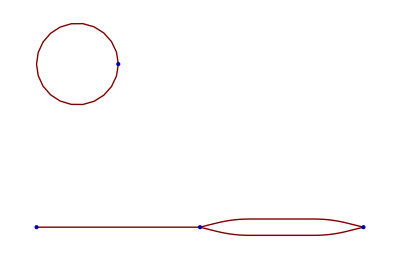

```mathematica
GraphPlot[{1->2,2->3,2->3,4->4}]
```

```mathematica
Cases[X3[[1]],{_,_},{1}]
Cases[X3[[2]],{_,_},{1}]
```

{}

{{A,r1},{A,s1}}

More advanced example: A[x]^2 A[y]^2

```mathematica
cf=op[CO[{A,i1},{A,i2},{A,j1},{A,j2}],{A,i1},{A,i2},{A,j1},{A,j2}]
```

op[CO[{A,i1},{A,i2},{A,j1},{A,j2}],{A,i1},{A,i2},{A,j1},{A,j2}]

Replace fields:

```mathematica
X1=sortDummies@replaceFieldsCO[cf];
```

Set sources to zero:

```mathematica
X2=setSourcesZero[X1,action,{}];
```

Deal with the composite operator:

```mathematica
X3[[1]]
integrateDeltas[%]
```

delta[r1,s1] delta[t1,u1] op[P[{A,r1},{A,s1}],P[{A,t1},{A,u1}]]

op[P[{A,s1},{A,s1}],P[{A,u1},{A,u1}]]

```mathematica
X3=X2/.op[CO[{A,i1_},{A,i2_},{A,i3_},{A,i4_}],rest___]:>delta[i1,i2]delta[i3,i4]op[rest]//integrateDeltas
```

op[P[{A,s1},{A,s1}],P[{A,u1},{A,u1}]]+2 op[P[{A,s1},{A,u1}],P[{A,s1},{A,u1}]]+op[{A,s1},{A,s1},P[{A,u1},{A,u1}]]+2 op[{A,s1},P[{A,s1},{A,u1}],{A,u1}]+op[P[{A,s1},{A,s1}],{A,u1},{A,u1}]+2 op[P[{A,s1},{A,u1}],{A,s1},{A,u1}]+op[{A,s1},{A,s1},{A,u1},{A,u1}]+op[{A,s1},P[{A,s1},{A,v1}],P[{A,u1},{A,w1}],V[{A,v1},{A,w1},{A,x1}],P[{A,x1},{A,u1}]]+op[P[{A,s1},{A,v1}],{A,s1},P[{A,u1},{A,w1}],V[{A,v1},{A,w1},{A,x1}],P[{A,x1},{A,u1}]]+2 op[P[{A,s1},{A,v1}],{A,u1},P[{A,s1},{A,w1}],V[{A,v1},{A,w1},{A,x1}],P[{A,x1},{A,u1}]]+op[P[{A,s1},{A,v1}],P[{A,s1},{A,w1}],P[{A,u1},{A,x1}],P[{A,y1},{A,u1}],V[{A,v1},{A,w1},{A,x1},{A,y1}]]+op[P[{A,r2},{A,t1}],P[{A,r2},{A,t2}],P[{A,s2},{A,u1}],V[{A,t2},{A,u1},{A,u2}],P[{A,u2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,s2}]]+op[P[{A,r2},{A,t1}],P[{A,r2},{A,t2}],V[{A,t2},{A,u1},{A,u2}],P[{A,u2},{A,s2}],P[{A,s2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,u1}]]+op[P[{A,r2},{A,t1}],P[{A,s2},{A,t2}],V[{A,u1},{A,t2},{A,u2}],P[{A,u2},{A,s2}],P[{A,r2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,u1}]]

Plotting is not working well, but the structure is ok:
Checked the expressions manually.

```mathematica
List@@X3
DSEPlot[#,fieldRules]&/@%
```

{op[P[{A,s1},{A,s1}],P[{A,u1},{A,u1}]],2 op[P[{A,s1},{A,u1}],P[{A,s1},{A,u1}]],op[{A,s1},{A,s1},P[{A,u1},{A,u1}]],2 op[{A,s1},P[{A,s1},{A,u1}],{A,u1}],op[P[{A,s1},{A,s1}],{A,u1},{A,u1}],2 op[P[{A,s1},{A,u1}],{A,s1},{A,u1}],op[{A,s1},{A,s1},{A,u1},{A,u1}],op[{A,s1},P[{A,s1},{A,v1}],P[{A,u1},{A,w1}],V[{A,v1},{A,w1},{A,x1}],P[{A,x1},{A,u1}]],op[P[{A,s1},{A,v1}],{A,s1},P[{A,u1},{A,w1}],V[{A,v1},{A,w1},{A,x1}],P[{A,x1},{A,u1}]],2 op[P[{A,s1},{A,v1}],{A,u1},P[{A,s1},{A,w1}],V[{A,v1},{A,w1},{A,x1}],P[{A,x1},{A,u1}]],op[P[{A,s1},{A,v1}],P[{A,s1},{A,w1}],P[{A,u1},{A,x1}],P[{A,y1},{A,u1}],V[{A,v1},{A,w1},{A,x1},{A,y1}]],op[P[{A,r2},{A,t1}],P[{A,r2},{A,t2}],P[{A,s2},{A,u1}],V[{A,t2},{A,u1},{A,u2}],P[{A,u2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,s2}]],op[P[{A,r2},{A,t1}],P[{A,r2},{A,t2}],V[{A,t2},{A,u1},{A,u2}],P[{A,u2},{A,s2}],P[{A,s2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,u1}]],op[P[{A,r2},{A,t1}],P[{A,s2},{A,t2}],V[{A,u1},{A,t2},{A,u2}],P[{A,u2},{A,s2}],P[{A,r2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,u1}]]}

{-Graphics-+^-1,-Graphics-+2^-1,-Graphics-+^,-Graphics-+2^,-Graphics-+^,-Graphics-+2^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+2^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

## Examples from DoFun2 article

Examples taken from DoFun 2 article and modified where necessary.

### 4.1 Derivation of DSEs OK

```mathematica
setFields[{phi},{{psi,psib}}]
```

```mathematica
doDSE[{{phi,phi},{phi,phi,phi,phi}},{phi,phi}]
```

op[S[{phi,i1},{phi,i2}]]-1/2 op[P[{phi,r1},{phi,s1}],S[{phi,i1},{phi,i2},{phi,r1},{phi,s1}]]-1/6 op[S[{phi,i1},{phi,r1},{phi,s1},{phi,t1}],P[{phi,r1},{phi,u1}],P[{phi,s1},{phi,v1}],P[{phi,w1},{phi,t1}],V[{phi,i2},{phi,u1},{phi,v1},{phi,w1}]]

```mathematica
twoPointPhi=doDSE[{{phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b}}]
```

op[S[{phi,a},{phi,b}]]-1/2 op[P[{phi,r1},{phi,s1}],S[{phi,a},{phi,b},{phi,r1},{phi,s1}]]-1/6 op[S[{phi,a},{phi,r1},{phi,s1},{phi,t1}],P[{phi,r1},{phi,u1}],P[{phi,s1},{phi,v1}],P[{phi,w1},{phi,t1}],V[{phi,b},{phi,u1},{phi,v1},{phi,w1}]]

```mathematica
twoPointPsi=doDSE[{{psi,psib},{psib,psib,psi,psi}},{{psib,a},{psi,b}}]
```

op[S[{psi,b},{psib,a}]]+op[P[{psi,s1},{psib,r1}],S[{psib,a},{psib,r1},{psi,s1},{psi,b}]]-1/2 op[S[{psib,a},{psib,r1},{psi,s1},{psi,t1}],P[{psi,u1},{psib,r1}],P[{psi,s1},{psib,v1}],P[{psi,t1},{psib,w1}],V[{psib,v1},{psib,w1},{psi,b},{psi,u1}]]

```mathematica
setFields[{},{{psi,psib}},{{phi,phib}}]
```

```mathematica
twoPointMixed=doDSE[{{phi,phib},{psi,psib},{psib,psi,phib,phi},{phib,phib,phi,phi},{psib,psib,psi,psi}},{{phi,b},{phib,a}},specificFieldDefinitions->{phi,phib,{psi,psib}}]
```

op[S[{phi,b},{phib,a}]]-op[P[{phi,r1},{phib,s1}],S[{phib,a},{phib,s1},{phi,b},{phi,r1}]]+op[P[{psi,s1},{psib,r1}],S[{psib,r1},{psi,s1},{phib,a},{phi,b}]]

### 4.2 Derivation of RGEs OK

```mathematica
setFields[{phi}]
```

```mathematica
doRGE[{{phi,phi},{phi,phi,phi,phi}},{}]
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,s1},{phi,r1}]]

```mathematica
doRGE[{{phi,phi},{phi,phi,phi,phi}},{phi,phi}]
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,i1},{phi,i2},{phi,t1},{phi,u1}]]

```mathematica
threeR=doRGE[{{phi,phi},{phi,phi,phi}},{phi,phi,phi}];
```

```mathematica
threeRPnot=doRGE[{{phi,phi},{phi,phi,phi}},{phi,phi,phi},tDerivative->False]
```

op[P[{phi,r1},{phi,s1}],V[{phi,i2},{phi,s1},{phi,t1}],P[{phi,t1},{phi,u1}],V[{phi,i3},{phi,v1},{phi,u1}],P[{phi,w1},{phi,v1}],V[{phi,i1},{phi,r1},{phi,w1}]]

### 4.3 (Graphical) Rpresentation of the output of doRGE and doDSE OK

```mathematica
shortExpression[op[S[{W,i},{W,k},{W,l}],P[{W,k},{W,ks}],P[{W,l},{W,ls}],V[{W,ks},{W,ls},{W,j}]]]
```

S_(W W W)^(i k l) Γ_(W W W)^(ks ls j) Δ_(W W)^(k ks) Δ_(W W)^(l ls)

```mathematica
shortExpression[op[S[{W,i},{W,k},{W,l}],P[{W,k},{W,ks}],dR[{W,ks},{W,ms}],P[{W,ms},{W,m}],P[{W,l},{W,ls}],V[{W,m},{W,ls},{W,j}]],FontSize->20,Bold]
```

∂_t R_(W W)^(ks ms) S_(W W W)^(i k l) Γ_(W W W)^(m ls j) Δ_(W W)^(k ks) Δ_(W W)^(l ls) Δ_(W W)^(ms m)

```mathematica
RGEPlot[doRGE[{{phi,phi},{phi,phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b}}]]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ |  |

```mathematica
RGEPlot[doRGE[{{phi,phi},{phi,phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b}}],{{phi,Black}}]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ |  |

### 4.4 Algebraic expressions OK

```mathematica
addIndices[{flavor,{i,j,k,l,m,n}}]
```

{dummyNames[flavor]→{i,j,k,l,m,n},dummyNames[type]→{i,j,l,m,n},dummyNames[adj]→{a,b,c,d,e,f,g,h,i,j},dummyNames[lor]→{μ,ν,ρ,σ,τ,α,β,γ,δ,ϵ}}

```mathematica
setFields[{phi}]
```

```mathematica
defineFieldsSpecific[{phi[momentum,type]}];
```

Warning: defineFieldsSpecific should not be used anymore. Use setFields instead.

```mathematica
addIndices[{type,{i,j,l,m,n}}];
```

```mathematica
P[phi[p1_,i_],phi[p2_,j_],explicit->True]:=delta[type,i,j]/(Z[k,p1^2]p1^2+R[k,p1^2])
dR[phi[p1_,i_],phi[p2_,j_],explicit->True]:=delta[type,i,j] dR[k,p1^2]
V[phi[p1_,i_],phi[p2_,j_],phi[p3_,k_],phi[p4_,l_],explicit->True]:=-lambda delta[type,i,l] delta[type,j,k]-lambda delta[type,i,k] delta[type,j,l]-lambda delta[type,i,j] delta[type,k,l]
```

```mathematica
twoR=doRGE[{{phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b}}]
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,a},{phi,b},{phi,t1},{phi,u1}]]

```mathematica
fourR=doRGE[{{phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b},{phi,c},{phi,d}}];
```

```mathematica
Plus@@getAE[twoR,{{phi,a,0,i},{phi,b,0,j}}];
Plus@@getAE[fourR,{{phi,a,0,i},{phi,b,0,j},{phi,c,0,l},{phi,d,0,m}}];
```

```mathematica
integrateDeltas[delta[type,j,1] delta[type,j,1] Plus@@getAE[twoR,{{phi,a,0,i},{phi,b,0,j}}]]/.dim[type]:>Ntype
```

-(lambda delta[type,i,j] dR[k,q1^2])/((R[k,q1^2]+q1^2 Z[k,q1^2])^2)-(lambda Ntype delta[type,i,j] dR[k,q1^2])/(2 (R[k,q1^2]+q1^2 Z[k,q1^2])^2)

```mathematica
integrateDeltas[delta[type,i,1] delta[type,j,1] delta[type,l,1] delta[type,m,1] Plus@@getAE[fourR,{{phi,a,0,i},{phi,b,0,j},{phi,c,0,l}, {phi,d,0,m}}]]/.dim[type]:>Ntype
```

-(24 lambda^2 dR[k,q1^2])/((R[k,q1^2]+q1^2 Z[k,q1^2])^3)-(3 lambda^2 Ntype dR[k,q1^2])/((R[k,q1^2]+q1^2 Z[k,q1^2])^3)

### O(N) model BROKEN: broken phase

#### 5.1 Introduction OK

```mathematica
actionONSymbolic={{phi,10,even}};
```

```mathematica
actionONSTrunc2={{phi,4,even}};
```

```mathematica
setFields[{phi}]
```

```mathematica
defineFieldsSpecific[{phi[momentum,type]}];
```

```mathematica
setFields[{phi}]
```

```mathematica
actionONPotential=convertAction[1/2 (q^2 Z[q^2]+R[k]) op[phi[q,a],phi[-q,a]]+U[phi]];
```

```mathematica
fieldStyleON={{phi,Black}};
```

#### 5.1.1 Symmetric regime OK

```mathematica
zeroPoint=doRGE[actionONSymbolic,{}];
twoPoint=doRGE[actionONSymbolic,{phi,phi}];
fourPoint=doRGE[actionONSymbolic,{phi,phi,phi,phi}];
sixPoint=doRGE[actionONSymbolic,{phi,phi,phi,phi,phi,phi}];
```

```mathematica
P[phi[p1_,a_],phi[p2_,b_],explicit->True]:=(delta[type,a,b])/(Z[p1^2]+R[p1^2,k]);
dR[phi[p1_,a_],phi[p2_,b_],explicit->True]:=delta[type,a,b] dR[p1^2,k];
```

```mathematica
actionON2=convertAction[1/2 (p^2 Z[p^2]+R[k])op[phi[p,i],phi[-p,i]]+lambda2/8op[phi[p,i],phi[q,i],phi[r,j],phi[-p-q-r,j]]];
```

```mathematica
V[phi[p1_,i_],phi[p2_,j_],phi[p3_,l_],phi[p4_,m_],explicit->True]=getFR[actionON2,{phi[p1,i],phi[p2,j],phi[p3,l],phi[p4,m]}]/deltam[p1+p2+p3+p4]//Expand;
```

```mathematica
zeroPointAlg=Plus@@getAE[zeroPoint,{}]//integrateDeltas
```

(dim[type] dR[q1^2,k])/(2 (R[q1^2,k]+Z[q1^2]))

```mathematica
twoPointAlg=Plus@@getAE[twoPoint,{{phi,i1,p1,i},{phi,i2,p2,j}}]//integrateDeltas
```

-(lambda2 delta[type,i,j] dR[q1^2,k])/((R[q1^2,k]+Z[q1^2]) (R[(p1+p2+q1)^2,k]+Z[(p1+p2+q1)^2]))-(lambda2 delta[type,i,j] dim[type] dR[q1^2,k])/(2 (R[q1^2,k]+Z[q1^2]) (R[(p1+p2+q1)^2,k]+Z[(p1+p2+q1)^2]))

```mathematica
fourPointAlg=Plus@@getAE[fourPoint,{{phi,i1,0,i},{phi,i2,0,j},{phi,i3,0,l},{phi,i4,0,m}}]/.V[a___]:>0/;Length@{a}>4//integrateDeltas//Simplify
```

-1/((R[q1^2,k]+Z[q1^2])^3)lambda2^2 (delta[type,i,m] delta[type,j,l]+delta[type,i,l] delta[type,j,m]+delta[type,i,j] delta[type,l,m]) (8+dim[type]) dR[q1^2,k]

#### 5.1.2 (Spontaneously) Broken O(N) symmetry in the ground state BROKEN

```mathematica
defineFieldsSpecific[{phi[momentum,type],phi0[momentum,type]}];
actionON2=convertAction[1/2 (p^2 Z[p^2]+R[k]) op[phi[p,i],phi[-p,i]]+lambda2b/8 op[op[phi[p,i],phi[q,i]]-op[phi0[p,i],phi0[q,i]],op[phi[r,j],phi[-p-q-r,j]]-op[phi0[r,j],phi0[-p-q-r,j]]]];
```

Warning: defineFieldsSpecific should not be used anymore.

convertAction::undefinedField: There is an undefined field or a field without specified indices in the expression. Use defineFieldsSpecific to define this field properly.

The field(s) in this expression is/are {phi,phi0}.

```mathematica
setFields[{phi,phi0}]
```

```mathematica
actionON2=convertAction[1/2 (p^2 Z[p^2]+R[k]) op[phi[p,i],phi[-p,i]]+lambda2b/8 op[op[phi[p,i],phi[q,i]]-op[phi0[p,i],phi0[q,i]],op[phi[r,j],phi[-p-q-r,j]]-op[phi0[r,j],phi0[-p-q-r,j]]]];
```

```mathematica
P[phi[p1_,a_],phi[p2_,b_],explicit->True]:=delta[type,a,1] delta[type,b,1]/(Z[p1^2] p1^2+R[p1^2,k]+2 rho0 lambda2b)+(delta[type,a,b]-delta[type,a,1] delta[type,b,1])/(Z[p1^2] p1^2+R[p1^2,k]);
```

```mathematica
dR[phi[p1_,a_],phi[p2_,b_],explicit->True]:=delta[type,a,b] dR[p1^2,k];
```

```mathematica
V[phi[p1_,i_],phi[p2_,j_],phi[p3_,k_],phi[p4_,l_],explicit->True]=getFR[actionON2,{phi[p1,i],phi[p2,j],phi[p3,k],phi[p4,l]},symmetry->broken]/deltam[p1+p2+p3+p4]//Expand;
```

```mathematica
zeroPointAlg=Plus@@getAE[zeroPoint,{}]//integrateDeltas
```

-dR[q1^2,k]/(2 (R[q1^2,k]+q1^2 Z[q1^2]))+(dim[type] dR[q1^2,k])/(2 (R[q1^2,k]+q1^2 Z[q1^2]))+dR[q1^2,k]/(2 (2 lambda2b rho0+R[q1^2,k]+q1^2 Z[q1^2]))

```mathematica
fourPointTrunc2=doRGE[actionONSTrunc2,{phi,phi,phi,phi}];
```

```mathematica
fourPointT2Alg=Plus@@getAE[fourPointTrunc2,{{phi,i1,0,i},{phi,i2,0,j},{phi,i3,0,l},{phi,i4,0,m}}]//integrateDeltas;
```

```mathematica
dimLessRulesON={R[q1^2,k]:>q1^2 r[y],rho0:>Z[q1^2]^(-1) kappa k^(d-2),lambda2b:>Z[q1^2]^2 lambda2 k^(4-d),dR[q1^2,k]:>q1^2 dtr[y],q1:>Sqrt[y] k,dq1:>k^2/2/q1};
```

```mathematica
angleInt[d_]:=4v[d];
fourPointT2Algy=Simplify[(angleInt[d] dq1 q1^(d-1) integrateDeltas[delta[type,i,1] delta[type,j,1] delta[type,l,1] delta[type,m,1] fourPointT2Alg]//.dimLessRulesON),d∈Integers]
```

6 k^(4-d) lambda2^2 y^(d/2) dtr[y] v[d] Z[k^2 y]^4 (1/(y^3 (r[y]+Z[k^2 y])^3)-dim[type]/(y^3 (r[y]+Z[k^2 y])^3)-9/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^3))

```mathematica
integrateDeltas[delta[type,i,1] delta[type,j,1] delta[type,l,1] delta[type,m,1] (delta[type,i,j] delta[type,l,m]+delta[type,i,l] delta[type,j,m]+delta[type,i,m] delta[type,j,l])]//.dimLessRulesON
```

3

```mathematica
twoPointB=doRGE[actionONSTrunc2,{phi,phi},symmetry->broken];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
twoPointAlg=integrateDeltas[Plus@@getAE[twoPointB,{{phi,i1,0,i},{phi,i2,0,j}}]];
```

```mathematica
twoPointAlgProj=integrateDeltas[delta[type,i,1] delta[type,j,1] twoPointAlg]/.phi[0,i_]:>phi0[i]/.phi0[_]^2:>2 rho0
```

-(2 lambda2b^2 rho0 dR[q1^2,k])/((R[q1^2,k]+q1^2 Z[q1^2])^3)+(2 lambda2b^2 rho0 dim[type] dR[q1^2,k])/((R[q1^2,k]+q1^2 Z[q1^2])^3)+(lambda2b dR[q1^2,k])/(2 (R[q1^2,k]+q1^2 Z[q1^2])^2)-(lambda2b dim[type] dR[q1^2,k])/(2 (R[q1^2,k]+q1^2 Z[q1^2])^2)+(18 lambda2b^2 rho0 dR[q1^2,k])/((2 lambda2b rho0+R[q1^2,k]+q1^2 Z[q1^2])^3)-(3 lambda2b dR[q1^2,k])/(2 (2 lambda2b rho0+R[q1^2,k]+q1^2 Z[q1^2])^2)

```mathematica
twoPointAlgProjy=Simplify[#,Element[d,Integers]]&/@(angleInt[d] dq1 q1^(d-1) twoPointAlgProj//.dimLessRulesON//Expand)//Simplify
```

k^2 lambda2 y^(d/2) dtr[y] v[d] Z[k^2 y]^2 (1/(y^2 (r[y]+Z[k^2 y])^2)-dim[type]/(y^2 (r[y]+Z[k^2 y])^2)-3/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^2)+4 kappa lambda2 Z[k^2 y] (-1/(y^3 (r[y]+Z[k^2 y])^3)+dim[type]/(y^3 (r[y]+Z[k^2 y])^3)+9/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^3)))

```mathematica
twoPointAlgProjy/k^2/Z[k^2 y]/lambda2
```

y^(d/2) dtr[y] v[d] Z[k^2 y] (1/(y^2 (r[y]+Z[k^2 y])^2)-dim[type]/(y^2 (r[y]+Z[k^2 y])^2)-3/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^2)+4 kappa lambda2 Z[k^2 y] (-1/(y^3 (r[y]+Z[k^2 y])^3)+dim[type]/(y^3 (r[y]+Z[k^2 y])^3)+9/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^3)))

```mathematica
regRulesZ={r[y]:>(1/y-1) UnitStep[1-y],dtr[y]:>2/y UnitStep[1-y],Z[_]:>1};
```

```mathematica
Integrate[fourPointT2Algy/(-3 k^(4-d))/.regRulesZ,{y,0,∞},Assumptions->{d>0}]
```

-(8 lambda2^2 (1-9/(1+2 kappa lambda2)^3-dim[type]) v[d])/d

### Gross-Neveu model BROKEN? Sign changes

```mathematica
setFields[{},{{psi,psib}}]
```

```mathematica
defineFieldsSpecific[{{psi[momentum,dirac,flavor],psib[momentum,dirac,flavor]}}];
```

Warning: defineFieldsSpecific should not be used anymore. Use setFields instead.

```mathematica
actionGN=convertAction[diracM[q,a,b] (Z[q^2]+Rs[q^2,k]) op[psib[q,a,i],psi[q,b,i]]+gb/(2 Nf) op[psib[q1,a,i],psi[q2,a,i],psib[q3,b,j],psi[q3+q1-q2,b,j]]];
```

```mathematica
twoPoint=doRGE[actionGN,{psib,psi}];
fourPoint=doRGE[actionGN,{{psib,i1},{psib,i2},{psi,i3},{psi,i4}}];
```

```mathematica
FR2Point=getFR[actionGN,{psib[p1,a,i],psi[p2,b,j]}]
```

delta[flavor,i,j] deltam[-p1+p2] diracM[p1,a,b] Rs[p1^2,k]+delta[flavor,i,j] deltam[-p1+p2] diracM[p1,a,b] Z[p1^2]

```mathematica
FR4Point=getFR[actionGN,{psib[p1,a,i],psib[p2,b,j],psi[p3,c,m],psi[p4,d,l]}]
```

(gb delta[dirac,a,c] delta[dirac,b,d] delta[flavor,i,m] delta[flavor,j,l] deltam[-p1-p2+p3+p4])/Nf-(gb delta[dirac,a,d] delta[dirac,b,c] delta[flavor,i,l] delta[flavor,j,m] deltam[-p1-p2+p3+p4])/Nf

```mathematica
P[psi[p1_,a_,i_],psib[p2_,b_,j_],explicit->True]:=delta[flavor,i,j] diracM[p1,a,b]/p1^2/(Z[p1^2]+Rs[p1^2,k]);
V[psib[p1_,a_,i_],psib[p2_,b_,j_],psi[p3_,c_,m_],psi[p4_,d_,l_],explicit->True]=FR4Point/deltam[-p1-p2+p3+p4]//Expand;
```

Must be treated like a vertex -> Set momenta accordingly.

```mathematica
dR[psib[p1_,a_,i_],psi[p2_,b_,j_],explicit->True]:=diracM[p2,a,b] delta[flavor,i,j] dRs[p1^2,k];
```

```mathematica
addIndices[{{flavor,{i,j,k,l,m,n}},{dirac,{a,b,c,d,e,f,g,h}}}];
```

```mathematica
dimRules={dim[flavor]:>Nf,dim[dirac]:>dgamma};
diracRules={diracM[-p_,a_,b_]:>-diracM[p,a,b],diracM[p_,a_,a_]:>0,diracM[q_,a_,b_] diracM[q_,b_,c_]:>q^2 delta[dirac,a,c],diracM[q_,b_,a_] diracM[q_,c_,b_]:>q^2 delta[dirac,a,c],diracM[q_,a_,b_]^2:>q^2 delta[dirac,a,a]};
```

```mathematica
twoPointAlg=Plus@@getAE[twoPoint,{{psi,i2,p1,b,j},{psib,i1,p2,a,i}}]//Expand;
```

Sign changed compared to original.

```mathematica
FixedPoint[integrateDeltas[#]/.diracRules&,twoPointAlg/.{p1->0,p2->0}]
```

-(gb delta[flavor,i,j] diracM[q1,a,b] dRs[q1^2,k])/(Nf q1^2 (Rs[q1^2,k]+Z[q1^2])^2)

(gb delta[flavor,i,j] diracM[q1,a,b] dRs[q1^2,k])/(Nf q1^2 (Rs[q1^2,k]+Z[q1^2])^2)

Note that the order of fields is such to obtain the flow eqauation for V[psib[a], psib[b], psi[c], psi[d].

```mathematica
fourPointAlg=Plus@@getAE[fourPoint,{{psib,i1,0,b,j},{psib,i2,0,a,i},{psi,i4,0,d,m},{psi,i3,0,c,l}}];
```

Sign changed compared to original.

```mathematica
fourPointAlgSim=Simplify[FixedPoint[integrateDeltas[#]/.diracRules&,fourPointAlg]]
```

-((2 gb^2 (delta[dirac,a,d] delta[dirac,b,c] delta[flavor,i,m] delta[flavor,j,l]-delta[dirac,a,c] delta[dirac,b,d] delta[flavor,i,l] delta[flavor,j,m]) (-2+dim[dirac] dim[flavor]) dRs[q1^2,k])/(Nf^2 q1^2 (Rs[q1^2,k]+Z[q1^2])^3))

(2 gb^2 (delta[dirac,a,d] delta[dirac,b,c] delta[flavor,i,m] delta[flavor,j,l]-delta[dirac,a,c] delta[dirac,b,d] delta[flavor,i,l] delta[flavor,j,m]) (-2+dim[dirac] dim[flavor]) dRs[q1^2,k])/(Nf^2 q1^2 (Rs[q1^2,k]+Z[q1^2])^3)

```mathematica
fourPointAlgSimProj=FixedPoint[integrateDeltas[#]/.diracRules&,V[psib[p1,a,i],psib[p2,b,j],psi[p3,c,l],psi[p4,d,m],explicit->True]/gb fourPointAlgSim]/.dimRules;
lhs=integrateDeltas[V[psib[p1,a,i],psib[p2,b,j],psi[p3,c,l],psi[p4,d,m],explicit->True] V[psib[p1,a,i],psib[p2,b,j],psi[p3,c,l],psi[p4,d,m],explicit->True]/gb^2]/.dimRules;
```

Sign changed compared to original.

```mathematica
beta=fourPointAlgSimProj/lhs//Simplify
```

(2 gb^2 (-2+dgamma Nf) dRs[q1^2,k])/(Nf q1^2 (Rs[q1^2,k]+Z[q1^2])^3)

-(2 gb^2 (-2+dgamma Nf) dRs[q1^2,k])/(Nf q1^2 (Rs[q1^2,k]+Z[q1^2])^3)

```mathematica
dimLessRulesGN={Rs[q1^2,k]:>r[y] Z[q1^2],gb->g k^(2-d),dRs[q1^2,k]:>-2 y Z[q1^2] r'[y],q1:>Sqrt[y] k,dq1:>k^2/2/q1};
```

```mathematica
angleInt[d_]:=4v[d];
```

Sign changed compared to original.

```mathematica
betaDimLess=angleInt[d] dq1 q1^(d-1) beta//.dimLessRulesGN//Expand;
Simplify[betaDimLess,Assumptions->Element[d,Integers]]
```

-(8 g^2 k^(2-d) (-2+dgamma Nf) y^(-1+d/2) v[d] r'[y])/(Nf (1+r[y])^3 Z[k^2 y]^2)

(8 g^2 k^(2-d) (-2+dgamma Nf) y^(-1+d/2) v[d] r'[y])/(Nf (1+r[y])^3 Z[k^2 y]^2)

```mathematica
sixPoint=doRGE[actionGN,{psib,psib,psib,psi,psi,psi}];
```

```mathematica
sixPointAlg=Plus@@getAE[sixPoint,{{psib,i1,0,a1,j1},{psib,i2,0,a2,j2},{psib,i3,0,a3,j3},{psi,i4,0,a4,j4},{psi,i5,0,a5,j5},{psi,i6,0,a6,j6}}];
```

```mathematica
fourPointAlgFinMom=Plus@@getAE[fourPoint,{{psib,i1,p1,a,i},{psib,i2,p2,b,j},{psi,i3,p3,c,l},{psi,i4,p4,d,m}}];
```

```mathematica
fourPointAlgFinMomProj=FixedPoint[integrateDeltas[#]/.diracRules&,V[psib[p1,a,i],psib[p2,b,j],psi[p3,c,l],psi[p4,d,m],explicit->True]/gb fourPointAlgFinMom]/.dimRules;
betaFinMom=fourPointAlgFinMomProj/lhs;
```

```mathematica
betaFinMomDimLess=angleInt[d] dq1 q1^(d-1) betaFinMom//.dimLessRulesGN//Expand;
```

Sign changed compared to original.

```mathematica
betaDimLessLargeNf=Limit[Expand@betaFinMomDimLess,Nf->∞];
Simplify[betaDimLessLargeNf,Assumptions->Element[d,Integers]]
```

1/((1+r[y])^2 Z[k^2 y])4 g^2 k^(2-d) y^(-1+d/2) diracM[k √y,c$232806,e$232806] v[d] (-diracM[-p2-p3-k √y,e$232806,c$232806]/((p2+p3+k √y)^2 (Rs[(p2+p3+k √y)^2,k]+Z[(p2+p3+k √y)^2]))-diracM[-p2-p4-k √y,e$232806,c$232806]/((p2+p4+k √y)^2 (Rs[(p2+p4+k √y)^2,k]+Z[(p2+p4+k √y)^2]))) r'[y]

(4 g^2 k^(2-d) y^(-1+d/2) diracM[k √y,c$172825,f$172825] v[d] ((p1+p3+k √y)^2 diracM[-p2-p3-k √y,f$172825,c$172825] (Rs[(p1+p3+k √y)^2,k]+Z[(p1+p3+k √y)^2])+(p2+p3+k √y)^2 diracM[-p1-p3-k √y,f$172825,c$172825] (Rs[(p2+p3+k √y)^2,k]+Z[(p2+p3+k √y)^2])) r'[y])/((p1+p3+k √y)^2 (p2+p3+k √y)^2 (1+r[y])^2 (Rs[(p1+p3+k √y)^2,k]+Z[(p1+p3+k √y)^2]) (Rs[(p2+p3+k √y)^2,k]+Z[(p2+p3+k √y)^2]) Z[k^2 y])

# Development

## Order of derivatives for DoFR

The derivatives with getFR follow now the order of the arguments, viz., {1,2,3,4} corresponds to d4 d3 d2 d1.

```mathematica
setFields[{},{{psi,psibar}}]
```

```mathematica
defineFieldsSpecific[{psi[momentum,ind],psibar[momentum,ind]}]
```

{psi[momentum,ind],psibar[momentum,ind]}

```mathematica
action=convertAction[op[psibar[p1,i1],psibar[p2,i2],psi[p3,i3],psi[-p1-p2-p3-p4,i4]]f[i1,i2,i3,i4]]
```

f[dummy[1],dummy[2],dummy[3],dummy[4]] op[psibar[q$30315,dummy[1]],psibar[q$30316,dummy[2]],psi[q$30317,dummy[3]],psi[-q$30315-q$30316-q$30317-q$30318,dummy[4]]]

```mathematica
getFR[action,{psibar[q1,j1],psibar[q2,j2],psi[q3,j3],psi[q4,j4]}]
```

-f[j1,j2,j3,j4]+f[j1,j2,j4,j3]+f[j2,j1,j3,j4]-f[j2,j1,j4,j3]

## Introduce a sign function

--> Implemented with functions sf[] and getSign[].

The new sf function has to be considered in all derivatives:
derivField
derivVertex
derivPropagator
derivPropagatorRGE

Note that sf also needs to take into account other quantities in the trace.

### setFields

New functions to be defined:
setFields
fieldType

```mathematica
Clear@setFields
setFields::usage="Sets the properties of the fields of an action.\n
Syntax:
setFields[bosons, grassmann, complex] where the arguments are lists containing bosons, pairs of Grassmannian fields and pairs of bosonic complex fields.
Bosons are always single entries, while Grassmannian fields and bosonic complex fields come as pairs in lists. The components of pairs are defined as mutual anti-fields.\n
Example: Definition of a bosonic field A, a pair of anti-commuting fields c and cb and a pair of bosonic complex fields phi and phib.
setFields[{A}, {{c, cb}}, {{phi, phib}}];
bosonQ /@ {A, c, cb, phi, phib}
fermionQ /@ {A, c, cb, phi, phib}
antiComplexFieldQ /@ {A, c, cb, phi, phib}
antiField/@{A,c,cb,phi,phib}
";
setFields::noPair="The fermions and/or complex fields are not given as pairs. The input was `1` and `2`. Each should be of the form {{field1, anti-field1},...}.";
setFields::syntax="There was a problem with the syntax of setFields.";

(* some defaults *)
setFields[bosons_List]:=setFields[bosons,{},{}]
setFields[bosons_List,fermions_List]:=setFields[bosons,fermions,{}]
(* check syntax of fermionic and complex fields (need to be pairs) *)
setFields[bosons_List,fermions_List,complexFields_List]/;Not[And@@Flatten[MatchQ[#,{_,_}]&/@Join[fermions,complexFields]]]:=Message[setFields::noPair,fermions,complexFields];
setFields[bosons_List,fermions_List,complexFields_List]:=Module[{},

(* set the field types *)
(* difference to DoFun2: complex fields are their own types *)
(#/:fieldType[#]:=boson)&/@bosons;
(#/:fieldType[#]:=fermion)&/@fermions[[All,1]];
(#/:fieldType[#]:=antiFermion)&/@fermions[[All,2]];
(#/:fieldType[#]:=complex)&/@complexFields[[All,1]];
(#/:fieldType[#]:=antiComplex)&/@complexFields[[All,2]];
(* internally used dummy fields *)
$dummyFieldF/:fieldType[$dummyFieldF]:=fermion;
$dummyFieldAF/:fieldType[$dummyFieldAF]:=antiFermion;

(* set all fields to Head field: Not done, since this does not fully work as expected *)
(*(#/:Head[#]=field)&/@Flatten[{bosons,fermions,complexFields}];*)

(* set (anti-)commutating property *)
(* TODO: put this in the init *)
(#/:grassmannQ[#]=False)&/@Flatten[{bosons,complexFields}];
(#/:grassmannQ[#]=True)&/@Flatten[{fermions,$dummyFieldF,$dummyFieldAF}];

(* define the anti-fields *)
(antiField[#[[1]]]=#[[2]])&/@Transpose[{bosons,bosons}];
(antiField[#[[1]]]=#[[2]])&/@fermions;(antiField[#[[2]]]=#[[1]])&/@fermions;(antiField[#[[1]]]=#[[2]])&/@complexFields;(antiField[#[[2]]]=#[[1]])&/@complexFields;

]
(* default error handler *)
setFields[a___]:=Message[setFields::syntax,a];
```

Tests:

```mathematica
setFields[{A},{{psi,psibar}},{{phi,phibar}},{Q}]
```

setFields::syntax: There was a problem with the syntax of setFields.

```mathematica
setFields[{A},{{psi,psibar}},{phi,phibar}]
```

setFields::noPair: The fermions and/or complex fields are not given as pairs. The input was {{psi,psibar}} and {phi,phibar}. Each should be of the form {{field1, anti-field1},...}.

```mathematica
setFields[{A},{{psi,psibar}},{{phi,phibar}}]
```

```mathematica
fieldType/@{A,psi,psibar,phi,phibar}
```

{boson,fermion,antiFermion,complex,antiComplex}

```mathematica
antiField/@{A,psi,psibar,phi,phibar}
```

{A,psibar,psi,phibar,phi}

```mathematica
grassmannQ/@{A,psi,psibar,phi,phibar}
```

{False,True,True,False,False}

### Test basic auxiliary functions

Signs are represented by sf[a,b] where a is a single field and b a list of fields. If a is a Grassmann field, a minus sign appears for each Grassmann field in b. sf basically represent the sign introduced by moving the field a beyond the fields b.

```mathematica
setFields[{A,B},{{c,cb},{d,db}},{{phi,phib}}]
```

```mathematica
Clear@sf
(* no fields left *)
sf[a_,{}]:=1
(* delete double fields *)
sf[a_,b___List]/;Sort@b=!=Union[b]:=sf[a,b/.{m1___,n_,m2___,n_,m3___}:>{m1,m2,m3}]
(* delete non-Grassmann fields *)
sf[a_,b___List]/;Not[FreeQ[b[[All,1]],_?bosonQ|_?complexFieldQ|_?antiComplexFieldQ]]:=sf[a,DeleteCases[b,_?bosonQ|_?complexFieldQ|_?antiComplexFieldQ]]
(* if the first field is not Grassmann, then no sf is needed *)
sf[a_,b___List]/;bosonQ[a]||complexFieldQ[a]||antiComplexFieldQ[a]:=1
```

```mathematica
exp1={{A,i},{A,j},{phi,k},{c,l},{c,l},{cb,m}};
exp2={{phi,k},{c,l},{c,l},{cb,m}};
exp3={{phi,k},{c,l},{cb,m},{phi,n}};
```

If a field appears twice (which can happen if it appears in a propagator and a vertex), then delete that. It cannot lead to a sign.

```mathematica
sf[{cb,i1},exp1]
```

sf[{cb,i1},{{cb,m}}]

```mathematica
sf[{cb,i1},exp2]
```

sf[{cb,i1},{{cb,m}}]

```mathematica
sf[{cb,i1},exp3]
```

sf[{cb,i1},{{c,l},{cb,m}}]

```mathematica
sf[{cb,i1},{}]
```

1

No Grassman field as first argument:

```mathematica
sf[{A,i1},exp1]
```

1

Function to get the sign:

```mathematica
Clear@getSigns
getSigns[exp_]:=exp/.sf[f_?grassmannQ,l__]:>(-1)^Count[l,_?grassmannQ]
```

```mathematica
getSigns[sf[{cb,i1},exp1]]
```

-1

```mathematica
getSigns[sf[{cb,i1},exp2]]
```

-1

```mathematica
getSigns[sf[{cb,i1},exp3]]
```

1

```mathematica
getSigns[sf[{A,i1},exp2]]
```

1

## Diagram types

Extract number and multiplicities of vertices:

```mathematica
Clear[getVertexNumbers]
getVertexNumbers[n_?NumericQ a_]:=getVertexNumbers[a]
getVertexNumbers[a_op]:=Sort@Cases[a,V[v__]:>Length@{v},∞]
```

Define various diagram types:
The first entry specifies the number of loops, the second gives an ordered list of vertex multiplicities.

```mathematica
diagTypes=<|(* two-point *)
{1,{2,2}}->"oneLoop",
{1,{4}}->"tadpole",
{2,{4,3,3}}->"sunset",
{2,{4,4}}->"squint",
(* three-point *)
{1,{3,3,3}}->"triangle",
{1,{3,3,3}}->"triangle3",
{1,{3,4}}->"swordfish",
{1,{3,4}}->"swordfish3",
(* four-point *)
{1,{3,3,3,3}}->"box",
{1,{3,3,4}}->"triangle4",
{1,{4,4}}->"swordfish4",
{1,{3,5}}->"fivePoint4"|>;
```

Functions to determine the diagram type:

```mathematica
Clear@getDiagramType
getDiagramType[n_?NumericQ a_]:=getDiagramType[a]
getDiagramType[a_op]:=diagTypes[{getLoopNumber[a],getVertexNumbers[a]}]
```

Extract a certain diagram type:

```mathematica
Clear@extractDiagramType
extractDiagramType[diags_,type_String]:=Select[diags,getDiagramType[#]==type&]
```

Group diagrams by classes:

```mathematica
Clear@groupDiagrams
groupDiagrams[exp_]:=(Function[class,{class,extractDiagramType[exp,class]}]/@Values@diagTypes)/. {_,0}:>Sequence[]
```

Known classes:

```mathematica
$diagramTypes=Values@diagTypes
```

{oneLoop,tadpole,sunset,squint,triangle3,swordfish3,box,triangle4,swordfish4,fivePoint4}